## V1: I have simplified the vertices down to an effective b=2 theory (up to the explicit b factors)

```mathematica
Quit
```

```mathematica
(*1. Clear any old tasks from memory first*)
If[ValueQ[autoSaveTask],TaskRemove[autoSaveTask]];

(*2. Capture the exact notebook handle right now*)
thisNotebook=EvaluationNotebook[];

(*3. Start the background task (Set to 5 seconds for a quick test)*)
autoSaveTask=SessionSubmit[ScheduledTask[NotebookSave[thisNotebook];
(*Optional:Flash a quick status message in the window's bottom left bar*)CurrentValue[thisNotebook,WindowStatusArea]="Auto-saved: "<>DateString["Time"],180]];
```

```mathematica
(*SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]*)
SetDirectory["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\Routines"]
<<LRWDiagrams`
```

D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\Routines

```mathematica
<<LRWDiagrams`
```

## SpaceVertices definition

```mathematica
ClearAll[DD]
SetAttributes[DD,Orderless]
DD[0,0]:=0
Derivative[1,0][DD][0,0]:=1
Derivative[0,1][DD][0,0]:=1
Derivative[1,1][DD][0,0]:=1
Derivative[2,0][DD][0,0]:=1
Derivative[0,2][DD][0,0]:=1
```

```mathematica
ClearAll[Vγ1,Vγ1δ,Vγ1δ1,Vγ1δ2,Vγ1Minus,Vγg,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ21,Vγ22,Vγ2Minus,Vγ2Minus1,Vγ2Minus2,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vδψχ,Vχχ,g,b];

Vγ1[space_,time_]:= V[γ  ϕ[Subscript[x, space],Subscript[t, time]](1)ϕs[Subscript[x, space],Subscript[t, time+1]]ψs[Subscript[x, space],Subscript[t, time]]];

(*Vγ21[space_,time_]:= V[γ2 DD[ϕ[space,Subscript[t, time]]] χs[space,1,1,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]];
Vγ22[space_,time_]:= V[-γ2 DD[ϕ[space,Subscript[t, time]]](χs[space,1,1,Subscript[t, time]]χs[space,2,2,Subscript[t, time]])ϕs[space,Subscript[t, time+1]]];*)

Vγ2[space_,time_]:= V[γ2 DD[ϕ[Subscript[x, space],Subscript[t, time]]](χs[Subscript[x, space],1,2,Subscript[t, time]]+χs[Subscript[x, space],2,2,Subscript[t, time]])ϕs[Subscript[x, space],Subscript[t, time+1]]]; (*NOTICE THAT WE HAVE TWO POSSIBILITIES OF χs*)

Vγ2Minus1[space_,time_]:= V[-γ2 ϕ[Subscript[x, space],Subscript[t, time]]b DD[χs[Subscript[x, space],1,2,Subscript[t, time]]]ϕs[Subscript[x, space],Subscript[t, time+1]]]*
Vψχ[space-1.25,time+0.25];
Vγ2Minus2[space_,time_]:= V[-γ2 ϕ[Subscript[x, space],Subscript[t, time]] b2/2 DD[χs[Subscript[x, space],1,1,Subscript[t, time]],χs[Subscript[x, space],2,2,Subscript[t, time]]]ϕs[Subscript[x, space],Subscript[t, time+1]]]*
Vψχδ[space-1.25,time+0.25]Vψχδ[space-2.25,time-0.25];

Vψχ[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}];V[-g ψ[Subscript[x, space],Subscript[t, time]]χ[Subscript[x, space],Subscript[i, r],Subscript[α, r],Subscript[t, time]]]
];
Vψχδ[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}];V[-g ψ[Subscript[x, space],Subscript[t, time]]χ[Subscript[x, space],Subscript[i, r],Subscript[α, r],Subscript[t, time]]χs[Subscript[x, space],Subscript[i, r],Subscript[α, r],Subscript[t, time]]]
];

Vγg[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}]; V[γg g b ϕ[Subscript[x, space],Subscript[t, time]]χs[Subscript[x, space],1,2,Subscript[t, time]]ϕs[Subscript[x, space],Subscript[t, time+1]]χ[Subscript[x, space],1,Subscript[α, r],Subscript[t, time]](*χs[space,1,Subscript[α, r],Subscript[t, time]]*)]
];
```

## EvaluateVertices[]

```mathematica
ClearAll[EvaluateVertices];
Options[EvaluateVertices]={"print"->False
, "nγ1δ"->0
, "nγ2"->0
,"nγ2Minus"->0
,"δfields"->False
,"endTime"->0
,"initialTime"->0
,"evaluate"->True
,"Appendϕ0"->False};


EvaluateVertices[vertexList_,OptionsPattern[]]:= Module[ {i,j,el,locVertexList, endTime,evaluatedVertexList={} ,skipFirst=0},

(* Start by checking that vertexList is a List of Lists *)
If[Head[vertexList]=!=List || Head[vertexList[[1]]]=!=List,
Print[Style[" PLEASE, PROVIDE A LIST OF LISTS ",Red]];
Abort[]];



(* Loop over vertexList elements*)
For[el=1,el<=Length[vertexList],el++,


locVertexList=vertexList[[el]];

(* Then define the endTime variable if not provided by the user *)
If[ OptionValue["endTime"]==0,
(*TRUE*)
endTime =Length[locVertexList],
(*FALSE*)
endTime = OptionValue["endTime"];
];

skipFirst=0;

(* Loop over the elements of locVertexList and assign the (x,t) arguments *)
For[j=1,j<=Length[locVertexList],j++,

If[NumericQ[locVertexList[[j]]],
skipFirst=1;Continue[];
];

If[MatchQ[locVertexList[[j]],-_],
(*TRUE*)
locVertexList[[j]]=-(-locVertexList[[j]])[(*Subscript[x, j+OptionValue["initialTime"]]*)j+OptionValue["initialTime"]-skipFirst,j+OptionValue["initialTime"]-skipFirst],
(*FALSE*)
locVertexList[[j]]=locVertexList[[j]][(*Subscript[x, j+OptionValue["initialTime"]]*)j+OptionValue["initialTime"]-skipFirst,j+OptionValue["initialTime"]-skipFirst];
];
];(*End of For over j*)

AppendTo[evaluatedVertexList,If[OptionValue["Appendϕ0"],V[ϕs[Subscript[x, 0],Subscript[t, 1]]],1](Times@@locVertexList)];

];(*End of For over el*)

Return[evaluatedVertexList];
];
```

## GiveInteractionVertices[]

```mathematica
ClearAll[SpreadInteractions];
Options[SpreadInteractions]={"print"->False, "δψχ"->False,"Vγ2δ"->False,"endTime"->0};

SpreadInteractions[nInt_,OptionsPattern[]]:=Module[{comps,maxLen,padded,interactionVertices,i,jj,endTime,Vγ2correction=0},

If[nInt==0, Return[1]];

If[OptionValue["endTime"]==0,endTime=nInt+1,endTime=OptionValue["endTime"];];

If[OptionValue["Vγ2δ"],Vγ2correction=1,Vγ2correction=0];

interactionVertices=0;

For[jj=1,jj<=nInt,jj++,

comps=Join@@Permutations/@IntegerPartitions[jj];

If[OptionValue["print"],
Print[" The compositions of ", j, " are :\n ",comps]];

maxLen=Max[Length/@comps];
maxLen=endTime;

padded=PadRight[#,maxLen,0]&/@comps;
padded=DeleteDuplicates[Flatten[Permutations/@padded,1]];
(*padded=DeleteDuplicates[Select[padded,First[#]=!=0&]];*)

If[OptionValue["print"],
Print[" After padding with Zeros and removing leading zeros :\n ",padded]];

If[OptionValue["δψχ"],interactionVertices=Sum[Product[1/Factorial[ Abs[padded[[i,j]]-Vγ2correction] ] Product[Vδψχ[Subscript[x, ToExpression[ToString[j]<>ToString[nIndex]]],endTime-j+1],{nIndex,1,padded[[i,j]] }],{j,1,nInt(*this is equal to Length[padded[[i]]]*)}],
{i,1,Length[padded]}];
Return[interactionVertices];
];

interactionVertices+=Sum[Product[1/Factorial[ Abs[padded[[i,j]]-Vγ2correction] ] Product[Vψχ[Subscript[x, ToExpression[ToString[j]<>ToString[nIndex]]],endTime-j+1],{nIndex,1,padded[[i,j]] }],{j,1,maxLen(*this is equal to Length[padded[[i]]]*)}],
{i,1,Length[padded]}]
];
Return[interactionVertices];
];
```

```mathematica
ClearAll[GiveInteractionVertices];
Options[GiveInteractionVertices]={"print"->False, "nInteractions"->nInteractionVertices,"δfields"->False,"endTime"->endTime,"initialTime"->0};


GiveInteractionVertices[vertexList_List,options:OptionsPattern[]]/;Head[vertexList[[1]]]==List:=Flatten[GiveInteractionVertices[#,options]&/@vertexList];

GiveInteractionVertices[vertexList_,OptionsPattern[]]:= Module[ {i,j,el,locVertexList, endTime,nInteractions,VertexListWithInteractions={} },

(* Start by checking that vertexList is a List *)
If[Head[vertexList]=!=List ,
Print[Style[" PLEASE, PROVIDE A LIST ",Red]];
Abort[]
];
(*
(* Loop over vertexList elements*)
For[el=1,el<=Length[vertexList],el++,

locVertexList=vertexList[[el]];
If[OptionValue["print"],
Print[" Considering : ", locVertexList]];

(* Count if there already are some g present in the list and define the number of interactions available*)
nInteractions=OptionValue["nInteractions"]-Exponent[locVertexList,g];
If[OptionValue["print"],
Print[" Number of g already present = ", Exponent[locVertexList,g]];

Print[" Then: OptionValue[\"nInteractions\"]-Exponent[locVertexList,g] = ",nInteractions];];

(* Then define the endTime variable if not provided by the user *)
If[ OptionValue["endTime"]==0,
(*TRUE*)
endTime =(Cases[locVertexList,ϕs[_,Subscript[t,k_]]:>k,All][[1]]-1),
(*FALSE*)
endTime = OptionValue["endTime"];
];

(* Multiply the locVertexList with the interaction vertices*)
locVertexList=List@@(Plus@@Expand[locVertexList*
SpreadInteractions[nInteractions,"endTime"->endTime,"Vγ2δ"->True]
]
);

AppendTo[VertexListWithInteractions,locVertexList];

];(*End of For over el*)
*)

(* W A Y  M O R E  E F F I C I E N T  C O D E: *)
VertexListWithInteractions=Times[#,(SpreadInteractions[OptionValue["nInteractions"]-Exponent[#,g],"endTime"->(OptionValue["endTime"]+1-Exponent[#,g]),"Vγ2δ"->True])]&/@(vertexList);
VertexListWithInteractions=MapApply[List,Expand[VertexListWithInteractions]+el];

VertexListWithInteractions=Flatten[VertexListWithInteractions];

VertexListWithInteractions=DeleteElements[VertexListWithInteractions,{el}];

Return[VertexListWithInteractions];

];
```

#### Test

```mathematica
GiveInteractionVertices[{{1},{a}}]
```

{}

## Spreadγ[] UPDATED

### Old version updated

```mathematica
ClearAll[Spreadγ];
Options[Spreadγ]={"print"->False, "nγ1δ"->0, "nγ2"->0,"nγ2Minus"->0,"nγ2Minus2"->0,"nγg"->0,"δfields"->True,"endTime"->0,"initialTime"->0,"evaluate"->True,"observable"->"psi"};

Spreadγ[nγ1_,OptionsPattern[]]:=Module[{vertexList={},i,j,endTime},

If[OptionValue["endTime"]==0,endTime=nγ1+OptionValue["nγ1δ"]+OptionValue["nγ2"]+OptionValue["nγ2Minus"],endTime=OptionValue["endTime"];];

If[OptionValue["δfields"],
(* WITH δfields *)
vertexList=
Join[PadRight[{},(nγ1-OptionValue["nγ1δ"]),Vγ1]
(*,PadRight[{},OptionValue["nγ1δ"],Vγ1δ]*)
,PadRight[{},OptionValue["nγ2"],Vγ2δ]
,PadRight[{},OptionValue["nγ2Minus"],Vγ2Minus1]
,PadRight[{},OptionValue["nγg"],Vγg]
,PadRight[{},Floor[OptionValue["nγ2Minus2"]],Vγ2Minus2]
];
,
(* WITHOUT δfields*)
vertexList=Join[PadRight[{},(nγ1-OptionValue["nγ1δ"]),Vγ1],(*PadRight[{},OptionValue["nγ1δ"],Vγ1δ],*)PadRight[{},OptionValue["nγ2"],Vγ2],PadRight[{},OptionValue["nγ2Minus"],Vγ2Minus]];
];

If[OptionValue["print"],
Print[" The vertices are :\n ",vertexList]];



(* REMOVE STRINGS CONTAINING γs IN THE WRONG PLACES *)
vertexList=DeleteDuplicates[Select[Permutations@vertexList,Last[#]=!=Vγ1(*&&First[#]=!=Vγ1δ&&First[#]=!=Vγ2&&First[#]=!=Vγ2Minus*)&&First[#]=!=Vγ2Minus1&&First[#]=!=Vγ2Minus2&&First[#]=!=Vγg&&First[#]=!=Vγ2δ&&First[#]=!=Vγ2Minusδ&]];


If[OptionValue["print"],
Print[" After permutations and removing leading δχs's:\n ",vertexList]];


If[OptionValue["nγ2Minus"]>1,
vertexList=Prepend[#,1/OptionValue["nγ2Minus"]!]&/@vertexList;
];

If[OptionValue["evaluate"]==False,
Return[vertexList]];


For[i=1,i<=endTime,i++,

For[j=1,j<=Length[vertexList],j++,
vertexList[[j,i]]=vertexList[[j,i]][Subscript[x, i+OptionValue["initialTime"]],i+OptionValue["initialTime"]];
];
];


vertexList=Plus@@Apply[Times,vertexList,1];


Return[vertexList];

];
```

### Rework: no permutations anymore, but manual positioning. OPTIMIZED FOR MY SIMPLIFIED VERTICES

So far, this is implemented to work only up to 3Loop. The reason is that beyond that one should also consider different permutations of Vγ2Minus2 and Vγ2

```mathematica
ClearAll[SpreadγNew];
Options[SpreadγNew]={"print"->False,"observable"->"prop"};

SpreadγNew[nLoop_,OptionsPattern[]]:=Module[{vertexList={},string={},i,j,k,combFact},
(*Special Case: nLoop=1 *)
If[nLoop==1,
string={Vγ1};

If[OptionValue["observable"]=="psi",
AppendTo[string,Vγ1],
AppendTo[vertexList,{Vγg}]
];

AppendTo[string,Vγ2Minus1];

AppendTo[vertexList,string];

Return[vertexList];
];

(*General case: nγ>1*)

For[i=0,i<=Floor[(nLoop)/2],i++,(*Number of γ2Minus2''s*)

For[j=0,j<=(nLoop-HeavisideTheta[0.5-i]-2i),j++,(*Number of γg's*)

For[k=(nLoop-j-2*i)*HeavisideTheta[0.5-j-2*i](*It must be maximal if the others are 0*),k<=(nLoop-j-2*i),k++,(*Number of γ2Minus1''s*)

combFact=1/(i!j!k!);

string=Flatten[(
Join[
PadRight[{},k,Vγ2Minus1],
PadRight[{},i,Vγ2Minus2],
PadRight[{},j,Vγg],
PadLeft[{},(nLoop-j),Vγ1]
])
,2];

string=DeleteDuplicates[
Select[Permutations@string,
Last[#]=!=Vγ1
&&First[#]==Vγ1
&&If[j==0,#[[2]]==Vγ1,True]
&&#[[2]]=!=Vγ2Minus1
&&#[[2]]=!=Vγ2Minus2
&&If[#[[-1]]===Vγ2Minus1,#[[-2]]=!=Vγ1,True]
&&If[(k+2i)==(nLoop-j),#[[-1]]=!=Vγg,True]&]
];

string=Prepend[#,combFact]&/@string;

AppendTo[vertexList,string];

];(*End of For over i*)
];(*End of For over j*)
];(*End of For over k*)

vertexList=Flatten[vertexList,1];

vertexList=Replace[#,a__/;((Count[#,Vγ1]-Count[#,Vγ2Minus1]-2*Count[#,Vγ2Minus2])>0&&Count[#,Vγ2Minus2]>0):>Sequence[a,a/.Vγ2Minus2:>Sequence[Vγ2Minus2,Vγ2]],{0}]&/@vertexList;


If[OptionValue["observable"]=="psi",
vertexList=DeleteDuplicates[Table[Insert[#,Vγ1,i],{i,2,Length@#}]]&/@vertexList;
vertexList=Flatten[vertexList,1];
];



Return[vertexList];

];
```

#### Test

```mathematica
SpreadγNew[1,"observable"->"psi"]
```

{{Vγ1,Vγ1,Vγ2Minus1}}

```mathematica
SpreadγNew[2]
SpreadγNew[2,"observable"->"psi"]
```

{{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1,Vγ1,Vγg},{1,Vγ1,Vγg,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ2Minus2}}

{{1/2,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1},{1,Vγ1,Vγ1,Vγg},{1,Vγ1,Vγ1,Vγg,Vγ2Minus1},{1,Vγ1,Vγg,Vγ1,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2}}

```mathematica
SpreadγNew[3]
```

{{1/6,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/6,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ2Minus1},{1,Vγ1,Vγ1,Vγg},{1,Vγ1,Vγ1,Vγ2Minus1,Vγg},{1,Vγ1,Vγ1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγg,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγg},{1/2,Vγ1,Vγg,Vγg,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2},{1,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1},{1,Vγ1,Vγg,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγg,Vγ2Minus2}}

```mathematica
SpreadγNew[3]
```

{{1/6,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/6,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ2Minus1},{1,Vγ1,Vγ1,Vγg},{1,Vγ1,Vγ1,Vγ2Minus1,Vγg},{1,Vγ1,Vγ1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγg,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγg},{1/2,Vγ1,Vγg,Vγg,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2},{1,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1},{1,Vγ1,Vγg,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγg,Vγ2Minus2}}

# NEW ROUTINES

## exhaustiveReplace[]: a fusion of ReplaceList and ReplaceAll

```mathematica
ClearAll[exhaustiveReplace,exhaustiveReplaceOld]
(*

exhaustiveReplaceOld[expr_Plus,rules_]:=exhaustiveReplace[#,rules]&/@(expr);

exhaustiveReplaceOld[expr_,rules_]:=Module[{exprList,count=0,results,junk},

exprList=DeleteElements[List@@(expr+junk),{junk}];

results=Total@FixedPoint[
(count++;
DeleteElements[List@@(Total[Join@@Table[With[{replaced=Level[ReplaceList[e,rules],{1}]},If[replaced==={},{e},replaced]],{e,#}]]+junk),{junk}])&
,exprList,10];

Expand[results/(1*(count-1)!)]
]
*)


exhaustiveReplace[expr_Plus,rules_]:=exhaustiveReplace[#,rules]&/@(expr);

exhaustiveReplace[expr_,rules_]:=Module[{exprList,count=0,results,junk},

exprList=ReleaseHold[List@@(expr+Hold[0])];

results=Total@FixedPoint[
(count++;
ReleaseHold[List@@(Total[Join@@Table[With[{replaced=Level[ReplaceList[e,rules],{1}]},If[replaced==={},{e},replaced]],{e,#}]]+Hold[0])])&
,exprList,10];

Expand[results/((count-1)!)]
]
```

#### Test

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 1],Subscript[t, 1]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]}]
```

-δ[{},{}] χ[x_1,t_1] G_ϕ[x_1,x_1,t_1,t_1]

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]}]
```

-2 δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_1,x_3,t_1,t_3]

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 7],Subscript[t, 1]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]}]
```

-2 δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_1,x_7,t_1,t_1] G_ϕ[x_4,x_2,t_4,t_1]-2 δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_1,x_7,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3]-2 δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_7,t_4,t_1]

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]ϕ[Subscript[x, 6],Subscript[t, 1]]ϕs[Subscript[x, 7],Subscript[t, 1]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]}]
```

-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_7,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3] G_ϕ[x_6,x_2,t_1,t_1]-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_7,t_4,t_1] G_ϕ[x_6,x_2,t_1,t_1]-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_7,t_1,t_1] G_ϕ[x_4,x_2,t_4,t_1] G_ϕ[x_6,x_3,t_1,t_3]-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_7,t_4,t_1] G_ϕ[x_6,x_3,t_1,t_3]-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1] G_ϕ[x_6,x_7,t_1,t_1]-δ[{},{}]^3 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3] G_ϕ[x_6,x_7,t_1,t_1]

```mathematica
exhaustiveReplace[Normal@Series[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]a ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{b,0,4}],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]}];
Collect[%,b]
```

a δ[{},{}] G_ϕ[x_4,x_3,t_4,t_3]+b (a δ[{},{}]^2 G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a δ[{},{}]^2 G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3])+b^2 (2 a δ[{},{}]^3 G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a δ[{},{}]^3 G_ϕ[x_1,x_2,t_1,t_1]^2 G_ϕ[x_4,x_3,t_4,t_3])+b^3 (3 a δ[{},{}]^4 G_ϕ[x_1,x_2,t_1,t_1]^2 G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a δ[{},{}]^4 G_ϕ[x_1,x_2,t_1,t_1]^3 G_ϕ[x_4,x_3,t_4,t_3])+b^4 (4 a δ[{},{}]^5 G_ϕ[x_1,x_2,t_1,t_1]^3 G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a δ[{},{}]^5 G_ϕ[x_1,x_2,t_1,t_1]^4 G_ϕ[x_4,x_3,t_4,t_3])

#### Some speedtests

```mathematica
dotimes=100;

Do[exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}],{dotimes}]//AbsoluteTiming

Do[exhaustiveReplaceOld[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}],{dotimes}]//AbsoluteTiming
```

{0.0485776,Null}

{0.0006268,Null}

```mathematica
AbsoluteTiming[exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}]]

AbsoluteTiming[exhaustiveReplacelv[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}]]
```

{0.0010674,δ[{},{}]^2 G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]-δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+δ[{},{}]^2 G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3]-δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3]}

{0.0000658,exhaustiveReplacelv[ϕ[x_1,t_1] ϕ[x_4,t_4] ϕs[x_2,t_1] ϕs[x_3,t_3]-ϕ[x_1,t_1] ϕ[x_4,t_4] ϕs[x_2,t_1] ϕs[x_3,t_3] χ[x_1,t_1],{A_. ϕ[x_,a___,t1_]^(n_.) ϕs[y_,b___,t2_]^(n_.):>A G_ϕ[x,y,t1,t2]^n δ[{a},{b}]}]}

```mathematica
AbsoluteTiming[exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}]]

AbsoluteTiming[exhaustiveReplacelv[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]]+ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^n_.:>A Subscript[G, ϕ][x,y,t1,t2]^n δ[{a},{b}]}]]
```

{0.0006636,2 δ[{},{}]^2 G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]-δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+2 δ[{},{}]^2 G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3]-δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3]}

{0.0001852,exhaustiveReplacelv[2 ϕ[x_1,t_1] ϕ[x_4,t_4] ϕs[x_2,t_1] ϕs[x_3,t_3]-ϕ[x_1,t_1] ϕ[x_4,t_4] ϕs[x_2,t_1] ϕs[x_3,t_3] χ[x_1,t_1],{A_. ϕ[x_,a___,t1_]^(n_.) ϕs[y_,b___,t2_]^(n_.):>A G_ϕ[x,y,t1,t2]^n δ[{a},{b}]}]}

#### Tests with DD

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]DD[ϕs[Subscript[x, 2],Subscript[t, 1]]]ϕ[Subscript[x, 4],Subscript[t, 1]]ϕs[Subscript[x, 3],Subscript[t, 3]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}]
,A_.*ϕ[x_,a___,t1_]^n_.*DD[ϕs[y_,b___,t2_],F___]^m_.:>A n*m DD[Subscript[G, ϕ][x,y,t1,t2],F](ϕ[x,a,t1])^(n-1)*(DD[ϕs[y,b,t2],F])^(m-1) δ[{a},{b}]}]
```

-DD[G_ϕ[x_4,x_2,t_1,t_1]] δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_3,t_1,t_3]-DD[G_ϕ[x_1,x_2,t_1,t_1]] δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_4,x_3,t_1,t_3]

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]DD[ϕs[Subscript[x, 2],Subscript[t, 1]],ϕs[Subscript[x, 2],Subscript[t, 1]]]ϕs[Subscript[x, 5],Subscript[t, 1]]ϕ[Subscript[x, 4],Subscript[t, 1]],{A_.*ϕ[x_,a___,t1_]^n_.*ϕs[y_,b___,t2_]^m_.:>A n*m Subscript[G, ϕ][x,y,t1,t2](ϕ[x,a,t1])^(n-1)*(ϕs[y,b,t2])^(m-1) δ[{a},{b}],A_.*ϕ[x_,a___,t1_]^n_.*DD[ϕs[y_,b___,t2_],F___]^m_.:>A n*m DD[Subscript[G, ϕ][x,y,t1,t2],F](ϕ[x,a,t1])^(n-1)*(DD[ϕs[y,b,t2],F])^(m-1) δ[{a},{b}]}]
```

-2 DD[G_ϕ[x_1,x_2,t_1,t_1],G_ϕ[x_4,x_2,t_1,t_1]] δ[{},{}]^2 ϕs[x_5,t_1] χ[x_1,t_1]-2 DD[ϕs[x_2,t_1],G_ϕ[x_4,x_2,t_1,t_1]] δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_1,x_5,t_1,t_1]-2 DD[ϕs[x_2,t_1],G_ϕ[x_1,x_2,t_1,t_1]] δ[{},{}]^2 χ[x_1,t_1] G_ϕ[x_4,x_5,t_1,t_1]

```mathematica
exhaustiveReplace[-χ[Subscript[x, 1],Subscript[t, 1]]ϕ[Subscript[x, 1],Subscript[t, 1]]DD[{ϕs[Subscript[x, 2],Subscript[t, 1]],ϕs[Subscript[x, 3],Subscript[t, 3]]}]ϕ[Subscript[x, 4],Subscript[t, 1]],{A_.*ϕ[x_,a___,t1_]^n_.*DD[{ϕs[y_,b___,t2_],F_}]^m_.:>A n*m DD[{Subscript[G, ϕ][x,y,t1,t2],F}](ϕ[x,a,t1])^(n-1)*(DD[{ϕs[y,b,t2],F}])^(m-1) δ[{a},{b}],A_.*ϕ[x_,a___,t1_]^n_.*DD[{F_,ϕs[y_,b___,t2_]}]^m_.:>A n*m DD[{F,Subscript[G, ϕ][x,y,t1,t2]}](ϕ[x,a,t1])^(n-1)*(DD[{F,ϕs[y,b,t2]}])^(m-1) δ[{a},{b}]}]
```

-DD[{G_ϕ[x_1,x_2,t_1,t_1],G_ϕ[x_4,x_3,t_1,t_3]}] δ[{},{}]^2 χ[x_1,t_1]-DD[{G_ϕ[x_4,x_2,t_1,t_1],G_ϕ[x_1,x_3,t_1,t_3]}] δ[{},{}]^2 χ[x_1,t_1]

## Let us make the delta behave as we want & ExpandDelta

```mathematica
ClearAll[δ]
```

OrderLess

```mathematica
SetAttributes[δ,Orderless]
```

```mathematica
δ[1,2]===δ[2,1]
```

True

```mathematica
δ[{1},{2}]===δ[{2},{1}]
```

True

Single list is listless

```mathematica
δ[{a_},{b_}]:=δ[a,b]
```

```mathematica
δ[{1},{2}]
δ[{1,4},{5,2}]
```

δ[1,2]

δ[{1,4},{5,2}]

Void is 1

```mathematica
δ[{},{}]:=1
```

```mathematica
δ[{},{}]
```

1

SelfExpanding

```mathematica
ClearAll[ExpandDelta];
ExpandDelta/:ExpandDelta[list_List]:=ExpandDelta/@list;
ExpandDelta/:ExpandDelta[A_+b_.* B_]:=ExpandDelta[A]+ExpandDelta[b*B];

ExpandDelta/:ExpandDelta[A_]/;FreeQ[A,δ]:=A;

ExpandDelta/:ExpandDelta[A_. δ[{a1_,a2___},{b1_,b2___}]]:=δ[a1,b1]ExpandDelta[A δ[{a2},{b2}] ];
ExpandDelta/:ExpandDelta[A_. δ[a_,b_]]:=δ[a,b]ExpandDelta[A  ];
```

```mathematica
δ[{1},{2}]
ads a δ[{1,4},{5,2}] -δ[{x,y},{z,t}]δ[{r,s},{u,v}]
ExpandDelta[%]
```

δ[1,2]

a ads δ[{1,4},{5,2}]-δ[{r,s},{u,v}] δ[{x,y},{z,t}]

a ads δ[1,5] δ[2,4]-δ[r,u] δ[s,v] δ[t,y] δ[x,z]

## Reworking of WickContractionSpaceVerticesMODfaster[] WITH exhaustiveReplace HUGLY FASTER THAN BEFORE!!!

```mathematica
Do[With[{field=pair[[1]],delta=pair[[2]]},Evaluate[field]/:D[field[x___],field[],NonConstants->{field}]:=delta[x]],{pair,fields}];
```

Do::iterb: Iterator {pair,fields} does not have appropriate bounds.

```mathematica
dernumb=1;
D[ϕ[Subscript[x, 2],Subscript[t, 1]]^dernumb,{ϕ[],dernumb},NonConstants->{ϕ}]/dernumb!
```

D[ϕ[x_2,t_1],ϕ[],NonConstants→{ϕ}]

```mathematica
fields={{ϕ,δϕ},{ϕs,δϕs},{χ,δχ},{χs,δχs},{ψ,δψ},{ψs,δψs}};
ClearAll[#]&/@fields

Do[With[{field=pair[[1]],delta=pair[[2]]},Evaluate[field]/:D[field[x___],field[],NonConstants->{field}]:=delta[x]],{pair,fields}];

(*ϕ/:D[ϕ[x__],ϕ[],NonConstants->{ϕ}]:=δϕ[x]
ϕs/:D[ϕs[x__],ϕs[],NonConstants->{ϕs}]:=δϕs[x]

χ/:D[χ[x__],χ[],NonConstants->{χ}]:=δχ[x]
χs/:D[χs[x__],χs[],NonConstants->{χs}]:=δχs[x]

ψ/:D[ψ[x__],ψ[],NonConstants->{ψ}]:=δψ[x]
ψs/:D[ψs[x__],ψs[],NonConstants->{ψs}]:=δψs[x]*)
```

{Null,Null,Null,Null,Null,Null}

```mathematica
dernumb=3;
D[χs[Subscript[x, 2],Subscript[t, 1]]^dernumb,{χs[],dernumb},NonConstants->{χs}]/dernumb!
```

δχs[x_2,t_1]^3

```mathematica
dernumb=3;
D[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]],{ϕ[],dernumb},NonConstants->{ϕ}]/dernumb!
D[%,{ϕs[],dernumb},NonConstants->{ϕs}](*/dernumb!*)
```

1/6 b^3 ⅇ^(b ϕ[x_1,t_1] ϕs[x_2,t_1]) δϕ[x_1,t_1]^3 ϕs[x_2,t_1]^3

b^3 ⅇ^(b ϕ[x_1,t_1] ϕs[x_2,t_1]) δϕ[x_1,t_1]^3 δϕs[x_2,t_1]^3+3 b^4 ⅇ^(b ϕ[x_1,t_1] ϕs[x_2,t_1]) δϕ[x_1,t_1]^3 δϕs[x_2,t_1]^3 ϕ[x_1,t_1] ϕs[x_2,t_1]+3/2 b^5 ⅇ^(b ϕ[x_1,t_1] ϕs[x_2,t_1]) δϕ[x_1,t_1]^3 δϕs[x_2,t_1]^3 ϕ[x_1,t_1]^2 ϕs[x_2,t_1]^2+1/6 b^6 ⅇ^(b ϕ[x_1,t_1] ϕs[x_2,t_1]) δϕ[x_1,t_1]^3 δϕs[x_2,t_1]^3 ϕ[x_1,t_1]^3 ϕs[x_2,t_1]^3

I have to rework it: instead of contracting time slice by time slice, I use the definitions of each propagators with general space-time coordinates

```mathematica
ClearAll[WickContractionSpaceVerticesMODfasterLoc];
Options[WickContractionSpaceVerticesMODfasterLoc]={
"print"->False,
"fields"->FieldsNamesGenerator[{ϕ(*,χ,ψ*)}], 
"startingTime"->1, 
"endTime"->1,
"#vertices"->10,
"δrule"->True,
"δruleExternal"->True,
"\!\(\*SubscriptBox[\(n\), \(χ\)]\)"->(-1),
"\!\(\*SubscriptBox[\(n\), \(α\)]\)"->(0),
"maxContractions"->3,
"killψ"->False,
"SimplifyPropagators"->True,
"SimplifyGψ"->True,
"SimplifyLoops"->False,
"ReturnJustAction"->False,
"FreeAction"->FreeAction};

WickContractionSpaceVerticesMODfasterLoc[A_ +B_,opts:OptionsPattern[]]:=WickContractionSpaceVerticesMODfasterLoc[A,opts]+
WickContractionSpaceVerticesMODfasterLoc[B,opts];


WickContractionSpaceVerticesMODfasterLoc[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									NON Polynomials                             
##############################################################################*)


WickContractionSpaceVerticesMODfasterLoc[V[A_] *B_., OptionsPattern[]]:=Module[
{interactionPermutations={},locFields={},starFields={},deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,jj,l,timeIndex,ii,ss,DDflag=False,rule},

If[OptionValue["print"],DeleteFile[LogFile]];

z=V[A] B;

If[OptionValue["ReturnJustAction"],Return[z];];

locFields=OptionValue["fields"]⟦1⟧;starFields=OptionValue["fields"]⟦2⟧;deltaFields=OptionValue["fields"]⟦3⟧;deltaStarFields=OptionValue["fields"]⟦4⟧;


z=z+Hold[0];

For[l=1,l≤Length[locFields],l++,

If[FreeQ[z,locFields⟦l⟧],Continue[]];

If[!FreeQ[z,DD[a___]/;!FreeQ[{a},locFields⟦l⟧]||!FreeQ[{a},starFields⟦l⟧]],DDflag=True;,DDflag=False;];

If[OptionValue["print"],LogMessage[{"################## Contracting ",locFields⟦l⟧[x_,t_]," ##################"}]];

(*Zeroth contribution*)

zTemp1=Replace[z,{locFields⟦l⟧[___]->0},{1,7}];

contributions=zTemp1;

If[OptionValue["print"],LogMessage[{"Zeroth contribution: ",contributions}]];zTemp1=z;

For[ii=1,ii≤OptionValue["maxContractions"],ii++,

If[OptionValue["print"],LogMessage[{"Contraction order ",ii,": "}]];

zTemp1=Replace[zTemp1,{starFields⟦l⟧[a___]:>κ deltaStarFields⟦l⟧[a]},{1,8}];

If[zTemp1-z=!=0,
zTemp1=D[zTemp1,{κ,ii}]/(ii!)/.κ->0;
];

If[OptionValue["print"],LogMessage[{"Extraction of ",deltaStarFields⟦l⟧," at order ",ii,":\n ",zTemp1}]];

zTemp2=Replace[zTemp1,{locFields⟦l⟧[a___]:>κ deltaFields⟦l⟧[a]},{1,8}];

If[OptionValue["print"],LogMessage[{"Replacement: ",locFields⟦l⟧->κ deltaFields⟦l⟧,":\n ",zTemp2}]];

If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,ii}]/(ii!)/.κ->0;
];

If[OptionValue["print"],LogMessage[{"Extraction of ",deltaFields⟦l⟧," at order ",ii,":\n ",zTemp1}]];

If[zTemp1=!=0,

zTemp1=Expand[zTemp1];

rule=Flatten[{If[DDflag,{f_ DD[deltaStarFields⟦l⟧[y_,b___,t2_],g___]^(n_.) (deltaFields⟦l⟧[x_,a___,t1_])^(m_.):>f n m DD[Subscript[G, locFields[[l]]][x,y,t1,t2],g] DD[deltaStarFields⟦l⟧[y,b,t2],g]^(n-1) (deltaFields⟦l⟧[x,a,t1])^(m-1) δ[{a},{b}],f_. (deltaStarFields⟦l⟧[x_,a___,t1_])^(n_.) DD[deltaFields⟦l⟧[y_,b___,t2_],g___]^(m_.):>f n m DD[Subscript[G, locFields⟦l⟧][y,x,t1,t2],g] (deltaStarFields⟦l⟧[x,a,t1])^(n-1) DD[deltaFields⟦l⟧[y,b,t2],g]^(m-1) δ[{a},{b}]},{}],{f_. (deltaFields⟦l⟧[x_,a___,t1_])^(n_.) (deltaStarFields⟦l⟧[y_,b___,t2_])^(m_.):>f Subscript[G, locFields⟦l⟧][x,y,t1,t2] n m (deltaFields⟦l⟧[x,a,t1])^(n-1) (deltaStarFields⟦l⟧[y,b,t2])^(m-1) δ[{a},{b}]}}];

If[OptionValue["print"],LogMessage[{" Contration rule for field ",locFields⟦l⟧,": ",rule}];LogMessage[{"################################################################################################"}]];

If[OptionValue["print"],LogMessage[{" zTemp1 before exhaustiveReplace: ",zTemp1}];LogMessage[{"################################################################################################"}]];

zTemp2=exhaustiveReplace[zTemp1,rule];

If[OptionValue["print"],LogMessage[{"Contraction of ",locFields⟦l⟧,starFields⟦l⟧,"\n ",zTemp2}]];

zTemp1=Replace[zTemp2,{locFields⟦l⟧[___]->0,starFields⟦l⟧[___]->0},{1,5}];

];(*End of zTemp1=!=0*)

zTemp2=zTemp1/.locFields⟦l⟧[___]->0;

If[contributions-zTemp2=!=0&&zTemp2=!=0,
contributions+=zTemp2;
If[OptionValue["print"],LogMessage[{"Contribution #",ii,": ",zTemp2}]];
];

zTemp1=z;
];(*End of for over contributions*)

 z=contributions;

If[OptionValue["print"],LogMessage[{"Overall contributions: ",contributions}];LogMessage[{"################################################################################################"}]];

contributions=0;

(*BEGINNING OF SIMPLIFICATIONS*)
z=ExpandDelta[z];

If[OptionValue["print"],LogMessage[{"Expansion of the δ's: ",z}];LogMessage[{"################################################################################################"}]];

If[OptionValue["δrule"],z=z//.Σδrule;

If[OptionValue["print"],LogMessage[{"Application of the δrule: ",z}];LogMessage[{"################################################################################################"}]];];

z=ReleaseHold[z];

If[OptionValue["δruleExternal"],
z=ReleaseHold[Replace[z+Hold[0],term_ δ[a_,b_]/;NumericQ[b]&&!NumericQ[a]:>ReleaseHold[Hold[term/.a:>b]],{1}]];z=ReleaseHold[Replace[z+Hold[0],term_ δ[a_,b_]/;NumericQ[a]&&!NumericQ[b]:>ReleaseHold[Hold[term/.b:>a]],{1}]];z=z//.δ[a_,a_]->1;

If[OptionValue["print"],LogMessage[{"Application of the δruleExternal: ",z}];LogMessage[{"################################################################################################"}]];
];

z=Replace[z,{Subscript[n, χ]->OptionValue["\!\(\*SubscriptBox[\(n\), \(χ\)]\)"],Subscript[n, α]->OptionValue["\!\(\*SubscriptBox[\(n\), \(α\)]\)"]},{1,3}];
];(*End of For over fields *)

If[OptionValue["SimplifyLoops"],z=Replace[z,{Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],__]/;!FreeQ[a,action]&&!FreeQ[a,action]:>0,Subscript[G, ϕ][a_,a_,b_,c_]^n_.->0,Subscript[G, ϕ][a_,c_,b_,b_]^n_.->0},{1,2}];];

If[OptionValue["killψ"],z=z/.ψs[___,Subscript[t, a_]]/;a≤timeIndex:>0/.δψs[___,Subscript[t, a_]]/;a≤timeIndex:>0;];

Clear[locFields,starFields,deltaFields,deltaStarFields,contributions,zTemp1,zTemp2,κ,jj,l,timeIndex,ii,ss];

If[OptionValue["print"],LogMessage[{"Final result:\n ",z}];];

If[OptionValue["SimplifyPropagators"],z=SimplifyPropagators[z,"SimplifyGψ"->OptionValue["SimplifyGψ"]]];

If[OptionValue["print"],SystemOpen[LogFile]];

Return[z]
];

(*################################################################################
									Plynomials                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

(*WickContractionSpaceVerticesMODfasterLoc[A_ *B_, opts:OptionsPattern[]]:=
WickContractionSpaceVerticesMODfasterLoc[V[B] *A, opts];*)


WickContractionSpaceVerticesMODfasterLoc[A_ , OptionsPattern[]]:=Module[
{interactionPermutations={},locFields={},starFields={},deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,jj,l,timeIndex,ii,ss,DDflag=False,rule={}},

If[OptionValue["print"],DeleteFile[LogFile]];

z=A ;

If[OptionValue["ReturnJustAction"],Return[z];];

locFields=OptionValue["fields"]⟦1⟧;
starFields=OptionValue["fields"]⟦2⟧;
deltaFields=OptionValue["fields"]⟦3⟧;
deltaStarFields=OptionValue["fields"]⟦4⟧;


z=z+Hold[0];

contributions=0;

zTemp2=z;

For[l=1,l≤Length[locFields],l++,

If[FreeQ[z,locFields⟦l⟧],
(*Print[Style[Row[{"There is no field " ,locFields⟦l⟧}],Red]];*)Continue[]
];

If[OptionValue["print"],LogMessage[{"################## Contracting ",locFields⟦l⟧[x_,t_]," ##################"}]];

(*Zeroth contribution*)
zTemp1=Replace[z,{locFields⟦l⟧[___]->0},{1,7}];

contributions+=zTemp1;

If[OptionValue["print"],LogMessage[{"Zeroth contribution: ",contributions}]];

(*REMAINING contribution*)
If[!FreeQ[z,DD[a___]/;!FreeQ[{a},locFields⟦l⟧]||!FreeQ[{a},starFields⟦l⟧]],DDflag=True;,DDflag=False;];

(*Print["DDflag=",DDflag];*)

zTemp1=zTemp2;

rule=
Flatten[
{
If[DDflag,{f_ DD[starFields⟦l⟧[y_,b___,t2_],g___]^(n_.) (locFields⟦l⟧[x_,a___,t1_])^(m_.):>f n m DD[Subscript[G, locFields⟦l⟧][x,y,t1,t2],g] DD[starFields⟦l⟧[y,b,t2],g]^(n-1) (locFields⟦l⟧[x,a,t1])^(m-1) δ[{a},{b}]
,f_. (starFields⟦l⟧[x_,a___,t1_])^(n_.) DD[locFields⟦l⟧[y_,b___,t2_],g___]^(m_.):>f n m DD[Subscript[G, locFields⟦l⟧][y,x,t1,t2],g] (starFields⟦l⟧[x,a,t1])^(n-1) DD[locFields⟦l⟧[y,b,t2],g]^(m-1) δ[{a},{b}]},
(*FALSE*){}]
,{f_. (locFields⟦l⟧[x_,a___,t1_])^(n_.) (starFields⟦l⟧[y_,b___,t2_])^(m_.):>f Subscript[G, locFields⟦l⟧][x,y,t1,t2] n m (locFields⟦l⟧[x,a,t1])^(n-1) (starFields⟦l⟧[y,b,t2])^(m-1) δ[{a},{b}]}
}];

If[OptionValue["print"],LogMessage[{" Contration rule for field ",locFields⟦l⟧,": ",rule}];LogMessage[{"################################################################################################"}]];

If[OptionValue["print"],LogMessage[{" zTemp1 before exhaustiveReplace: ",zTemp1}];LogMessage[{"################################################################################################"}]];

zTemp2=exhaustiveReplace[ReleaseHold[zTemp1],rule];
(*zTemp2=zTemp2/.locFields⟦l⟧[___]:>0;*)

If[OptionValue["print"],LogMessage[{"Contribution of field ",locFields⟦l⟧,": ",zTemp2}];LogMessage[{"################################################################################################"}]];

];(*End of loop over fields*)

contributions+=zTemp2;

z=contributions;

If[OptionValue["print"],LogMessage[{"Overall contributions: ",contributions}];LogMessage[{"################################################################################################"}]];contributions=0;


(*BEGINNING OF SIMPLIFICATIONS*)
z=ExpandDelta[z];

If[OptionValue["print"],LogMessage[{"Expansion of the δ's: ",z}];LogMessage[{"################################################################################################"}]];

If[OptionValue["δrule"],z=z//.Σδrule;

If[OptionValue["print"],LogMessage[{"Application of the δrule: ",z}];LogMessage[{"################################################################################################"}]];];

z=ReleaseHold[z];

If[OptionValue["δruleExternal"],
z=ReleaseHold[ReplaceRepeated[z+Hold[0],term_ δ[a_,b_]/;NumericQ[b]&&!NumericQ[a]:>ReleaseHold[Hold[term δ[a,b]/.a:>b]](*,{1,2}*)]];(*z=ReleaseHold[Replace[z+Hold[0],term_ δ[a_,b_]/;NumericQ[a]&&!NumericQ[b]:>ReleaseHold[Hold[term δ[a,b]/.b:>a]],{1,2}]];*)
z=z//.δ[a_,a_]->1;

If[OptionValue["print"],LogMessage[{"Application of the δruleExternal: ",z}];LogMessage[{"################################################################################################"}]];
];

z=Replace[z,{Subscript[n, χ]->OptionValue["\!\(\*SubscriptBox[\(n\), \(χ\)]\)"],Subscript[n, α]->OptionValue["\!\(\*SubscriptBox[\(n\), \(α\)]\)"]},{1,3}];


If[OptionValue["SimplifyLoops"],z=Replace[z,{Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],__]/;!FreeQ[a,action]&&!FreeQ[a,action]:>0,Subscript[G, ϕ][a_,a_,b_,c_]^n_.->0,Subscript[G, ϕ][a_,c_,b_,b_]^n_.->0},{1,2}];];

If[OptionValue["killψ"],z=z/.ψs[___,Subscript[t, a_]]/;a≤timeIndex:>0/.δψs[___,Subscript[t, a_]]/;a≤timeIndex:>0;];

Clear[locFields,starFields,deltaFields,deltaStarFields,contributions,zTemp1,zTemp2,κ,jj,l,timeIndex,ii,ss];

If[OptionValue["print"],LogMessage[{"Final result:\n ",z}];];

If[OptionValue["SimplifyPropagators"],z=SimplifyPropagators[z,"SimplifyGψ"->OptionValue["SimplifyGψ"]]];

If[OptionValue["print"],SystemOpen[LogFile]];

Return[z]

];
```

#### tests

```mathematica
/;(!FreeQ[A,Exp]||!FreeQ[B,Exp])
```

```mathematica
WickContractionSpaceVerticesMODfasterLoc[ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]a,"maxContractions"->3,"print"->True,
"SimplifyLoops"->False,
"fields"->FieldsNamesGenerator[{ϕ(*,χ,ψ*)}]]
```

a G_ϕ[x_1,x_2,t_1,t_1]

```mathematica
WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->3,"print"->False,"SimplifyLoops"->False]
```

a+a b G_ϕ[x_1,x_2,t_1,t_1]+a b^2 G_ϕ[x_1,x_2,t_1,t_1]^2+a b^3 G_ϕ[x_1,x_2,t_1,t_1]^3

```mathematica
WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a ϕ[Subscript[x, 4],Subscript[t, 4]]ϕs[Subscript[x, 3],Subscript[t, 3]],"maxContractions"->3,"print"->False];
Collect[%,b]
```

a G_ϕ[x_4,x_3,t_4,t_3]+b (a G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_3,t_4,t_3])+b^2 (2 a G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_1,x_3,t_1,t_3] G_ϕ[x_4,x_2,t_4,t_1]+a G_ϕ[x_1,x_2,t_1,t_1]^2 G_ϕ[x_4,x_3,t_4,t_3])

```mathematica
WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]DD[ϕs[Subscript[x, 2],Subscript[t, 1]]]]]a,"maxContractions"->3,"print"->False]
```

a+a b DD[G_ϕ[x_1,x_2,t_1,t_1]]+a b^2 DD[G_ϕ[x_1,x_2,t_1,t_1]]^2+a b^3 DD[G_ϕ[x_1,x_2,t_1,t_1]]^3

```mathematica
WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a ϕ[Subscript[x, 4],Subscript[t, 4]]DD[ϕs[Subscript[x, 3],Subscript[t, 3]]],"maxContractions"->3,"print"->False];
Collect[%,b]
```

a DD[G_ϕ[x_4,x_3,t_4,t_3]]+b (a DD[G_ϕ[x_4,x_3,t_4,t_3]] G_ϕ[x_1,x_2,t_1,t_1]+a DD[G_ϕ[x_1,x_3,t_1,t_3]] G_ϕ[x_4,x_2,t_4,t_1])+b^2 (a DD[G_ϕ[x_4,x_3,t_4,t_3]] G_ϕ[x_1,x_2,t_1,t_1]^2+2 a DD[G_ϕ[x_1,x_3,t_1,t_3]] G_ϕ[x_1,x_2,t_1,t_1] G_ϕ[x_4,x_2,t_4,t_1])

SpeedTest		WAY FASTER!

```mathematica
WickContractionSpaceVerticesMODfasterLoc[b V[ϕ[Subscript[x, 1],Subscript[t, 1]]]ϕs[Subscript[x, 2],Subscript[t, 1]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]]

Internal`InheritedBlock[{δ},Clear[δ];
WickContractionSpaceVerticesMODfaster[V[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]]]


Internal`InheritedBlock[{δ},Clear[δ];
WickContractionSpaceVerticesMODfaster[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]]]
```

a b G_ϕ[x_1,x_2,t_1,t_1]

a b G_ϕ[x_1,x_2,t_1]

a+a b G_ϕ[x_1,x_2,t_1]+a b^2 G_ϕ[x_1,x_2,t_1]^2+a b^3 G_ϕ[x_1,x_2,t_1]^3+a b^4 G_ϕ[x_1,x_2,t_1]^4

```mathematica
AbsoluteTiming[Do[WickContractionSpaceVerticesMODfasterLoc[b V[ϕ[Subscript[x, 1],Subscript[t, 1]]]ϕs[Subscript[x, 2],Subscript[t, 1]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]],{200}]]

AbsoluteTiming[Do[WickContractionSpaceVerticesMODfasterLoc[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]],{200}]]

Internal`InheritedBlock[{δ},Clear[δ];
Do[WickContractionSpaceVerticesMODfaster[V[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]],{200}]//AbsoluteTiming]
```

{0.152964,Null}

{0.111106,Null}

{0.226092,Null}

```mathematica
AbsoluteTiming[Do[WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]],{200}]]

Internal`InheritedBlock[{δ},Clear[δ];
Do[WickContractionSpaceVerticesMODfaster[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]],{200}]//AbsoluteTiming]
```

{0.544728,Null}

{2.45109,Null}

```mathematica
WickContractionSpaceVerticesMODfasterLoc[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]]

Internal`InheritedBlock[{δ,ϕ,ϕs,x},Clear[δ,ϕ,ϕs,x];
WickContractionSpaceVerticesMODfaster[V[Exp[b ϕ[Subscript[x, 1],Subscript[t, 1]]ϕs[Subscript[x, 2],Subscript[t, 1]]]]a,"maxContractions"->4,"print"->False,
"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}]]
]
```

a+a b G_ϕ[x_1,x_2,t_1,t_1]+a b^2 G_ϕ[x_1,x_2,t_1,t_1]^2+a b^3 G_ϕ[x_1,x_2,t_1,t_1]^3+a b^4 G_ϕ[x_1,x_2,t_1,t_1]^4

a+a b G_ϕ[x_1,x_2,t_1]+a b^2 G_ϕ[x_1,x_2,t_1]^2+a b^3 G_ϕ[x_1,x_2,t_1]^3+a b^4 G_ϕ[x_1,x_2,t_1]^4

DD

```mathematica
V[-g χ[Subscript[x, 16],Subscript[1, 32223],Subscript[α, 32223],Subscript[t, 16]] ψ[Subscript[x, 16],Subscript[t, 16]]] DD[χs[Subscript[x, 3],1,2,Subscript[t, 3]]]

WickContractionSpaceVerticesMODfasterLoc[%,"endTime"->(endTime),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]
```

DD[χs[x_3,1,2,t_3]] V[-g χ[x_16,1_32223,α_32223,t_16] ψ[x_16,t_16]]

-g DD[G_χ[x_16,x_3,t_16,t_3]] ψ[x_16,t_16]

```mathematica
V[-g χ[Subscript[x, 16],Subscript[1, 32223],Subscript[α, 32223],Subscript[t, 16]] ψ[Subscript[x, 16],Subscript[t, 16]]] χs[Subscript[x, 2],1,2,Subscript[t, 2]] ϕs[Subscript[x, 3],Subscript[t, 4]] χ[Subscript[x, 2],1,Subscript[α, 86388],Subscript[t, 2]] ψs[Subscript[x, 1],Subscript[t, 2]]DD[χs[Subscript[x, 3],1,2,Subscript[t, 3]]]

WickContractionSpaceVerticesMODfasterLoc[%,"endTime"->(endTime),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(n),"killψ"->False,"maxContractions"->10]
```

DD[χs[x_3,1,2,t_3]] V[-g χ[x_16,1_32223,α_32223,t_16] ψ[x_16,t_16]] ϕs[x_3,t_4] χ[x_2,1,α_86388,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_2]

-g DD[G_χ[x_16,x_3,t_16,t_3]] δ[2,α_86388] ϕs[x_3,t_4] ψ[x_16,t_16] ψs[x_1,t_2] G_χ[x_2,x_2,t_2,t_2]-g DD[G_χ[x_2,x_3,t_2,t_3]] δ[2,α_86388] ϕs[x_3,t_4] ψ[x_16,t_16] ψs[x_1,t_2] G_χ[x_16,x_2,t_16,t_2]

Logic for kroneker delta

```mathematica
g[A,B]δ[A,2]
ReleaseHold[Replace[(%+Hold[0]),term_*δ[a_,b_]/;(NumericQ[b] && !NumericQ[a]):>ReleaseHold[Hold[term/.a:>b]],{1}]]
```

g[A,B] δ[2,A]

g[2,B]

## EvaluatePropagators

```mathematica
ClearAll[EvaluatePropagators];
EvaluatePropagators/:EvaluatePropagators[list_List]:=EvaluatePropagators/@list;
EvaluatePropagators/:EvaluatePropagators[A_+b_.* B_]:=EvaluatePropagators[A]+EvaluatePropagators[b*B];

(*EvaluatePropagators/:EvaluatePropagators[a_* b_]:=EvaluatePropagators[a]EvaluatePropagators[b];
EvaluatePropagators/:EvaluatePropagators[a_.* Subscript[G, f_][p___]^n_]:=EvaluatePropagators[a* Subscript[G, f][p]^(n-1)]EvaluatePropagators[Subscript[G, f][p]];*)


EvaluatePropagators/:EvaluatePropagators[a_]/;FreeQ[a,Subscript[G, _][_,_,_,_]]:=a;
EvaluatePropagators/:EvaluatePropagators[a_^n_]/;!FreeQ[a,Subscript[G, _]]:=EvaluatePropagators[a]EvaluatePropagators[a^(n-1)];

EvaluatePropagators/:EvaluatePropagators[a_.*Subscript[G, χ][x1_,x2_,t1_,t2_]]:=ReleaseHold[Hold[EvaluatePropagators[a Subscript[G, χ][x1,x2,t2]]/.t1->t2]]
EvaluatePropagators/:EvaluatePropagators[a_.*DD[Subscript[G, χ][x1_,x2_,t1_,t2_],A___]]:=ReleaseHold[Hold[EvaluatePropagators[a DD[Subscript[G, χ][x1,x2,t2],A]]/.t1->t2]]

EvaluatePropagators/:EvaluatePropagators[a_.*Subscript[G, ψ][x1_,x2_,t1_,t2_]]:=ReleaseHold[Hold[EvaluatePropagators[a Subscript[G, ψ][x1,x1,{t1,t2}]]/.x1->x2]]


(*EvaluatePropagators/:EvaluatePropagators[a_.*Subscript[G, ϕ][___,t2_]^n_. Subscript[G, ϕ][___,t2_]^m_.]:=0
EvaluatePropagators/:EvaluatePropagators[a_.*Subscript[G, ϕ][x1_,x2_,t1_,t2_]^n_.]:=EvaluatePropagators[a Subscript[G, ϕ][x1,x2,t2]^n]*)
```

```mathematica
ClearAll[Subscript[G, ψ][__,0]];
Subscript[G, ψ][__,0]:=0
Subscript[G, ψ][__,{a_,a_}]:=0
Subscript[G, ψ][__,{Subscript[t, a_],Subscript[t, b_]}]/;b>a:=0
```

```mathematica
Subscript[G, ψ][__,0]
```

0

```mathematica
DD[Subscript[G, χ][x1,x2,t1,t2],Subscript[G, χ][x3,x4,t4,t5]]
EvaluatePropagators[%]
```

DD[G_χ[x1,x2,t1,t2],G_χ[x3,x4,t4,t5]]

DD[G_χ[x1,x2,t2],G_χ[x3,x4,t5]]

#### Test

```mathematica
EvaluatePropagators[-a+a b Subscript[t, 1] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 2],Subscript[t, 1],Subscript[t, 1]]Subscript[G, χ][1,2,Subscript[t, 2],Subscript[t, 1]]-a b^2 (Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 2],Subscript[t, 1],Subscript[t, 1]])^2 Subscript[G, ψ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2],Subscript[t, 1]]]
```

-a+EvaluatePropagators[a b t_1 G_ϕ[x_1,x_2,t_1,t_1] G_χ[1,2,t_1]]+EvaluatePropagators[-a b^2 G_ϕ[x_1,x_1,t_1,t_1]^2 G_ψ[x_1,x_1,{t_2,t_1}]]

```mathematica
EvaluatePropagators[{-a,a b Subscript[t, 1] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 2],Subscript[t, 1],Subscript[t, 1]]Subscript[G, χ][1,2,Subscript[t, 2],Subscript[t, 1]]-a b^2 (Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 2],Subscript[t, 1],Subscript[t, 1]])^2 Subscript[G, ψ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2],Subscript[t, 1]]}]
```

{-a,EvaluatePropagators[a b t_1 G_ϕ[x_1,x_2,t_1,t_1] G_χ[1,2,t_1]]+EvaluatePropagators[-a b^2 G_ϕ[x_1,x_1,t_1,t_1]^2 G_ψ[x_1,x_1,{t_2,t_1}]]}

## DRAWING routine update

```mathematica
ClearAll[DrawFromContractionGeneral,x];
Options[DrawFromContractionGeneral]={"pointSize"->0.015,"ArrowHeadSize"->0.05,"ψsLength"->0.4,"print"->False,"showEndLines"->False,"ImageSize"->Medium,"export"->False,"exportDirectory"->"myFile.pdf","initialIndex"->1};

(*DrawFromContractionGeneral[exp_List,opts:OptionsPattern[]]:=(DrawFromContractionGeneral[#,opts]&/@(exp));*)

DrawFromContractionGeneral[exp_,OptionsPattern[]]:=Module[{locExp,terms,i,pureProp, weight, dots,plot},

If[OptionValue["print"],DeleteFile[LogFile]];  (*Place at the top of the notebook*)

locExp=exp/.V[a___]->a;
(* I want to check if terms is a list of lists (which means that exp conatained a sum, i.e. multiple diagrams)*)
If[!Head[locExp] ===List,
(* TRUE: if it is not a List of lists, let's make it so *)
locExp={locExp}
,
(*FALSE*)
If[Head[locExp] ===Plus,
(* True: make sure that each term does not contain sums*)
locExp=List@@(locExp);
Print[Style[Row[{"Some of them are sums!!"}],Red]]; 
](*End of IF on Plus*);

](*End of IF on List*);


plot={};

For[i=1,i<=Length[locExp],i++,

terms=locExp[[i]];

If[terms==0 ,
Print[Style[Row[{"!!ZERO at position ",i,"!!"}],Red]]; 
(*Abort[];*)
AppendTo[plot,0];
Continue[];
];

If[!OptionValue["showEndLines"], 
terms=terms/.χs[__]->1;
];

terms=List @@ (terms)/.Times->List;

If[OptionValue["print"],
LogMessage[{terms}]];

pureProp=DeleteElements[terms,{-1,b,b^n_?NumericQ,b2,g,g̃,Subscript[g, γ],γ,γ1,γ2,γg^n_.,-g,-g̃,-Subscript[g, γ],-γ,-γ1,-γ2,-γg^n_.,g^n_?NumericQ,g̃^n_?NumericQ,Subscript[g, γ]^n_?NumericQ,γ^n_?NumericQ,γ1^n_?NumericQ,γ2^n_?NumericQ}];
pureProp=DeleteCases[pureProp,_?NumericQ];

weight=Times@@DeleteElements[terms,pureProp];

pureProp=pureProp/.{
DD[ϕs[Subscript[x, a_],Subscript[t, c_]] Subscript[F_, χ][Subscript[x, d_],Subscript[x, b_],Subscript[t, e_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, e]],Subscript[F, χ][Subscript[x, d],Subscript[x, b-0.1],Subscript[t, e]],ϕs[Subscript[x, a-0.1],Subscript[t, c]]},DD[ Subscript[G_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]], Subscript[F_, χ][Subscript[x, d_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c]],Subscript[G, χ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]],Subscript[F, χ][Subscript[x, d],Subscript[x, b-0.1],Subscript[t, c]]},DD[χs[Subscript[x, d_],A___,Subscript[t, e_]] Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, b-0.1],Subscript[x, b],Subscript[t, c-1]],Subscript[F, ϕ][Subscript[x, a],Subscript[x, b-0.1],Subscript[t, c]],χs[Subscript[x, d-0.1],A,Subscript[t, e]]},DD[χs[Subscript[x, a_],A___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],χs[Subscript[x, a-0.1],A,Subscript[t, c]]},
DD[χs[Subscript[x, a_],A___,Subscript[t, c_]],χs[Subscript[x, a_],B___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],δχs[Subscript[x, a-0.1],A,Subscript[t, c]] δχs[Subscript[x, a-0.1],B,Subscript[t, c]]},
DD[{χs[Subscript[x, a_],A___,Subscript[t, c_]],χs[Subscript[x, a_],B___,Subscript[t, c_]]}]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],δχs[Subscript[x, a-0.1],A,Subscript[t, c]] δχs[Subscript[x, a-0.1],B,Subscript[t, c]]},DD[δχs[Subscript[x, a_],A___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],δχs[Subscript[x, a-0.1],A,Subscript[t, c]]},
DD[Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, a+0.2],Subscript[x, a],Subscript[t, c]],Subscript[F, ϕ][Subscript[x, a+0.2],Subscript[x, b],Subscript[t, c]]},
DD[Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>{Δ[Subscript[x, b-0.2],Subscript[x, b],Subscript[t, c]],Subscript[F, χ][Subscript[x, a],Subscript[x, b-0.2],Subscript[t, c]]}};

pureProp=Flatten@(pureProp/.{δχs[Subscript[x, a_],___,Subscript[t, c_]]:>δχs[Subscript[x, a],Subscript[t, c]],χs[Subscript[x, a_],___,Subscript[t, c_]]:>χs[Subscript[x, a],Subscript[t, c]],χ[Subscript[x, a_],___,Subscript[t, c_]]:>χ[Subscript[x, a],Subscript[t, c]]});

If[OptionValue["print"],
LogMessage[{"The propagators are\n ",pureProp}]];

(*Print[pureProp];*)

dots=Flatten[pureProp//.{
Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]:>{Style[{a+0.54,c},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,c},Disk[{0,0},0.05],Black]},Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,c},Disk[{0,0},0.05],Black]},χ[Subscript[x, a_],___,Subscript[t, c_]]:>{Style[{a+0.54,c},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,c},Disk[{0,0},0.05],Black]},Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],0]/;NumericQ[a]:>{Style[{a+0.54,1},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,1},Disk[{0,0},0.05],Black]},Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],0]/;NumericQ[a]:>{Style[{a,1},Disk[{0,0},0.05],Black],Style[{b,1},Disk[{0,0},0.05],Black],Style[{a,1.5},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,0.7},Disk[{0,0},0.05],White,EdgeForm[None]]},

Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]/;NumericQ[a]:>{Style[{a,c},Disk[{0,0},0.05],Black]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]/;NumericQ[a]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{a,IntegerPart[c-0.5]},Disk[{0,0},0.05],Black],Style[{a+0.3,c-0.5},Disk[{0,0},0.05],White,EdgeForm[None]]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]/;NumericQ[a]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,IntegerPart[c-0.5]},Disk[{0,0},0.05],Black]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, a_],0]/;NumericQ[a]:>{Style[{a+0.54,1},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,1},Disk[{0,0},0.05],Black]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],0]/;NumericQ[a]:>{Style[{a,1},Disk[{0,0},0.05],Black],Style[{b,1},Disk[{0,0},0.05],Black],Style[{a,1.5},Disk[{0,0},0.05],White,EdgeForm[None]],Style[{a,0.7},Disk[{0,0},0.05],White,EdgeForm[None]]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, a_],0]/;NumericQ[a]:>{Style[{a,1},Disk[{0,0},0.05],Black],Style[{a,1},Disk[{0,0},0.05],Black],Style[{a+0.3,1-0.5},Disk[{0,0},0.05],White,EdgeForm[None]]},Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],0]/;NumericQ[a]:>{Style[{a,1},Disk[{0,0},0.05],Black],Style[{b,1},Disk[{0,0},0.05],Black]},

ϕ[Subscript[x, a_],Subscript[t, c_]]/;NumericQ[a]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{a+0.3,c-0.5},Disk[{0,0},0.05],White,EdgeForm[None]]},
ϕs[Subscript[x, a_],Subscript[t, c_]]/;NumericQ[a]:>{Style[{a-0.1,c+0.2},Disk[{0,0},0.05],White,EdgeForm[None]]},

Δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,c},Disk[{0,0},0.05],Black]},ψs[Subscript[x, a_],Subscript[t, c_]]:>{Style[{a-0.1,c-0.8},Disk[{0,0},0.05],White,EdgeForm[None]]}}
];(* Flatten for dots*)

pureProp=pureProp/.{
(Subscript[F_, χ]^n_)[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,c},{a,c},n,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]:>{Style[FindArc[{a+0.5,c},{a,c},4,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,c},{a,c},4,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]],Style[FindArc[{a+0.5,c},{a,c},-4,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,c},{a,c},-4,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]]},
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},(b-a-0.2*HeavisideTheta[a-b]),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,c},{a,c},(b-a-0.2*HeavisideTheta[a-b]),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]],

Subscript[F_, χ][Subscript[x, a_],Subscript[x, a_],0]:>{Style[FindArc[{a+0.5,1},{a,1},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,1},{a,1},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]],Style[FindArc[{a+0.5,1},{a,1},-2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,1},{a,1},-2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]]},
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],0]:>Style[FindArc[{b,1},{a,1},1.1(b-a),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,1},{a,1},1.1(b-a),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Darker[Green]],

Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]^n_:>Style[FindArc[{b,IntegerPart[c-0.5]},{a,c},n,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,IntegerPart[c-0.5]},{a,c},n,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red],
Subscript[F_, ϕ][Subscript[x, out],Subscript[x, a_],Subscript[t, c_]]:>Style[Line[{{a+0.13,c+0.13},{a,c}}],Arrowheads[{0,.03}],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]:>Style[Arrow[{{a-0.13,c-0.13},{a,c}}],Arrowheads[{0,.03,0}],Red],

Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, a_],Subscript[t, c_]]:>{Style[FindArc[{a,IntegerPart[c-0.5]},{a,c},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,IntegerPart[c-0.5]},{a,c},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red]},
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,IntegerPart[c-0.5]},{a,c},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,IntegerPart[c-0.5]},{a,c},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red],

Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],0]^n_:>Table[Style[FindArc[{b,1},{a,1},(b-a+0.9)(-1)^j,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,1},{a,1},(b-a+0.9)(-1)^j,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red],{j,1,n}],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, a_],0]:>{Style[FindArc[{a+0.5,1},{a,1},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,1},{a,1},2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red],Style[FindArc[{a+0.5,1},{a,1},-2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{a+0.5,1},{a,1},-2,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red]},
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],0]:>Style[FindArc[{b,1},{a,1},(b-a+0.9),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[1]],FindArc[{b,1},{a,1},(b-a+0.9),"ArrowHeadSize"->OptionValue["ArrowHeadSize"]][[2]],Red],

(Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],{Subscript[t, c_],Subscript[t, d_]}])^(n_.):>Style[FindArc[{a,d},{a,c},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]]⟦1⟧,FindArc[{a,d},{a,c},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]]⟦2⟧,Blue],(*Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],{Subscript[t, c_],Subscript[t, d_]}]:>Style[FindArc[{a,c},{a,d},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]]⟦1⟧,FindArc[{a,c},{a,s},1,"ArrowHeadSize"->OptionValue["ArrowHeadSize"]]⟦2⟧,Blue],*)

Δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[Line[{{b,c},{a,c}}],Black,Dashed],


χs[Subscript[x, a_],___,Subscript[t, c_]]^n_:>Table[Style[Arrow[{{a,c},{a-0.2,c+0.1*Sin[π ii/n]}}],Arrowheads[{0,.03}],Darker[Green]],{ii,1,n}],
χs[Subscript[x, a_],___,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.2,c}}],Arrowheads[{0,.03}],Darker[Green]],
δχs[Subscript[x, a_],___,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.2,c}}],Arrowheads[{0,.03}],Darker[Green],Dashed],

δχs[Subscript[x, a_],___,Subscript[t, c_]]^n_:>Table[Style[Arrow[{{a,c},{a-0.2,c+0.1*Sin[π ii/n]}}],Arrowheads[{0,.03}],Darker[Green],Dashed],{ii,1,n}],
χ[Subscript[x, a_],___,Subscript[t, c_]]:>Style[Arrow[{{a+0.2,c},{a,c}}],Arrowheads[{0,0.03,0}],Darker[Green]],

ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.2,c+0.2}}],Arrowheads[{0,.03}],Red],
ϕ[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a-0.13,c-0.13},{a,c}}],Arrowheads[{0,.03,0}],Red],

ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c(*IntegerPart[c-1]*)},{a,c(*IntegerPart[c-1]*)+OptionValue["ψsLength"]}}],Arrowheads[{0,.03}],Blue],
ψ[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c(*IntegerPart[c-1]*)-OptionValue["ψsLength"]},{a,c(*IntegerPart[c-1]*)}}],Arrowheads[{0,.03,0}],Blue],
δψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.7}}],Arrowheads[{0,.03}],Blue,Dashed]};

pureProp=Flatten[pureProp];

If[OptionValue["print"],
LogMessage[{"They will be drawn as\n ",pureProp}]];
	(*dots=Flatten[pureProp//.{Style[Arrow[{{a_,c_},{b_,d_}}],___,color_]/;(IntegerQ[a*b*c*d]&&color=!=Blue):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{b-0.1,d},Disk[{0,0},0.05],White,EdgeForm[None]]},
Style[Line[{{a_,c_},{b_,c_}}],Black,Dashed]:>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,c},Disk[{0,0},0.05],Black]}}];*)

AppendTo[plot,ListPlot[dots,
PlotLabel-> Row[{ToString[i+OptionValue["initialIndex"]-1]<>": ",weight}],
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->{1,1}-0.2,
PlotStyle->{PointSize[OptionValue["pointSize"]]},
Prolog->pureProp,
ImagePadding->{{10,10},{10,10}},
PlotRangeClipping->False,
ImageSize->OptionValue["ImageSize"]]
];

];(*End of Loop*)

If[OptionValue["print"],SystemOpen[LogFile]];

If[OptionValue["export"],
Export[OptionValue["exportDirectory"],plot(*Row[plot,"\n"]*)];
];

Return[Row[plot]];
]
```

## RemoveGaps[]

```mathematica
ClearAll[RemoveGaps];

RemoveGaps[expr_]:=Module[{i,terms,temp1},
terms=expr;
For[i=1,i<=10,i++,
While[(FreeQ[terms,Subscript[x, i]]),
temp1=terms/.Subscript[x, a_]/;(a>i):>Subscript[x, a-1];
If[temp1===terms, Break[],terms=temp1]
];
];
For[i=1,i<=10,i++,
While[(FreeQ[terms,Subscript[t, i]]),
temp1=terms/.Subscript[t, a_]/;(a>i):>Subscript[t, a-1];
If[temp1===terms, Break[],terms=temp1]
];
];

terms
]
```

## DDeatsG UPDATE: IF IT WORKS, UPDATE .m file (done)

```mathematica
ClearAll[DDeatsG];

DDeatsG[exp_]:=Module[{terms,tlist,temp1,i},


If[Head[exp]=!=Times,
Print[Style["NOT A PRODUCT OF TERMS",Red]];
Return[0];
];

(*terms=exp//.DD[Subscript[G, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]->-1/γ2δ[Subscript[x, a],Subscript[x, b]]δt[Subscript[t, c]]//.DD[Subscript[G, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]->-δ[Subscript[x, a],Subscript[x, b]]
//.Subscript[G, ψ][A___]δ[Subscript[x, a_],Subscript[x, b_]]/;(!FreeQ[{A},Subscript[x, b]]):>δ[Subscript[x, a],Subscript[x, b]]
//.F_[A___,Subscript[x, a_],B___]δ[Subscript[x, a_],Subscript[x, b_]]->F[A,Subscript[x, b],B]δ[Subscript[x, a],Subscript[x, b]]
/.δ[__]->1;*)


terms=exp//.A_. DD[Subscript[G, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>ReleaseHold[Hold[-(A δt[Subscript[t, c]])/γ2/.Subscript[x, b]->Subscript[x, a]]]//.A_.DD[Subscript[G, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]]:>ReleaseHold[Hold[-A δt[Subscript[t, c]]/.Subscript[x, b]->Subscript[x, a]]](*
//.δ[Subscript[x, a_],Subscript[x, b_],C___] F_[A___,Subscript[x, a_],B___]->F[A,Subscript[x, b],B] δ[Subscript[x, a],Subscript[x, b],C]//.δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]] Subscript[G, ψ][A___]/;!FreeQ[{A},Subscript[x, b]]&&!FreeQ[{A},Subscript[t, c]]:>δ[Subscript[x, a],Subscript[x, b],Subscript[t, c]]
/.δ[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]->δ[Subscript[x, a],Subscript[x, b]] δt[Subscript[t, c]]/.δ[__]->1*);

(* Why do I need this?
If[!FreeQ[terms,δt],
tlist=Select[List@@terms,Head[#]==δt&];
tlist=Union[tlist/.δt[Subscript[t, a_]]->a];
];


Print[terms];
For[i=Length[tlist],i>=1,i--,
terms=terms/.Subscript[t, a_]/;a>=tlist[[i]]:>Subscript[t, a-1];

Print[terms];
];*)

terms=terms/.δt[__]->1/.Subscript[G, ψ][A___]^n_->Subscript[G, ψ][A];

(* Eliminate useless gaps *)
For[i=1,i<=5,i++,
While[(FreeQ[terms,Subscript[x, i]]),
temp1=terms/.Subscript[x, a_]/;(a>i):>Subscript[x, a-1];
If[temp1===terms, Break[],terms=temp1]
];
];(* END OF FOR*)

Return[terms];
];
```

# DIAGRAMS FOR OBSERVABLES, i.e. γ_1

## 1-Loop:

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=1;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Spreadγ[nInteractionVertices+1-(nInteractionVertices-iii),"print"->False,"nγ1δ"->0,"nγ2Minus"->iii,"nγg"->(nInteractionVertices-iii),"evaluate"->False,"observable"->"g"],
{iii,0,nInteractionVertices}])
,1]
)
```

{{Vγ1,Vγg},{Vγ1,Vγ1,Vγ2Minus1}}

```mathematica
ΓString@OneLoopγListCoupling;
EvaluateVertices[{OneLoopγListCoupling}]
```

{V[ϕs[x_0,t_1]] {Vγ1}[x_2,2] {Vγ1,Vγ1}[x_1,1] {Vγ1,Vγ1,Vγ2Minus}[x_3,3] {Vγ1,Vγ2Minus,Vγ1}[x_4,4]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackbone

```mathematica
EvaluateVertices[OneLoopγListCoupling];

AbsoluteTiming[OneLoopBackbone=(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.0048894,b g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_45541,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2]-b γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}

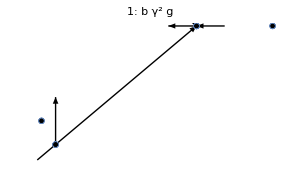
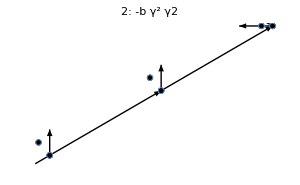

```mathematica
DrawFromContraction[(OneLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### OneLoop: contraction form OneLoopBackbone

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=1;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(*(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])(*Vψχ[Subscript[x,endTime+100],endTime+1]*)(*δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]]*))])
)*)
GiveInteractionVertices[List@@OneLoopBackbone];

AbsoluteTiming[OneLoop=Plus@@(WickContractionSpaceVerticesMODfaster[#,"endTime"->(3),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)(*/.ψs[__]->0*)/.V[b]->b]
```

{0.0723249,b g γ^2 ϕs[x_2,t_3] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3]+b g γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] ψs[x_1,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]+b g γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] ψs[x_2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]}

```mathematica
OneLoop/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

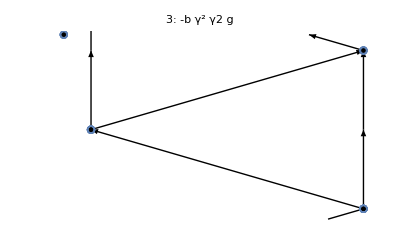
-Graphics--Graphics--Graphics-

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

## 2-Loop: VERTICES WITHOUT g

### TwoLoopBackbone

#### Generate TwoLoopγListCoupling

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Spreadγ[nInteractionVertices-(jjj),"print"->False,
"nγ1δ"->0,"nγ2Minus"->(nInteractionVertices-jjj-2iii),"nγ2Minus2"->(iii),"nγg"->(jjj),"evaluate"->False,"observable"->"g"],
{iii,0,Floor[(nInteractionVertices-jjj)/2]}],
{jjj,0,nInteractionVertices}])
,2]
)
```

{{Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγ2Minus1,Vγg},{Vγ1,Vγg,Vγ2Minus1}}

#### Contract ϕ in TwoLoopγListCoupling -> TwoLoopBackbone

```mathematica
EvaluateVertices[TwoLoopγListCoupling,"Appendϕ0"->True];

AbsoluteTiming[TwoLoopBackbone=(Total@(Internal`InheritedBlock[{δ,ϕ,ϕs,x},Clear[δ,ϕ,ϕs,x];
WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%]))]
```

{0.0298185,-b^2 g γ γ2 γg DD[χs[x_3,1,2,t_3]] ϕs[x_3,t_4] χ[x_2,1,α_27344,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]-b^2 g γ γ2 γg DD[χs[x_2,1,2,t_2]] ϕs[x_3,t_4] χ[x_3,1,α_57552,t_3] χs[x_3,1,2,t_3] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]-1/2 b2 γ^2 γ2 DD[χs[x_3,1,1,t_3],χs[x_3,2,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]+b^2 γ^2 γ2^2 DD[χs[x_3,1,2,t_3]] DD[χs[x_4,1,2,t_4]] ϕs[x_4,t_5] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]+b^2 γ^2 γ2^2 DD[χs[x_2,1,2,t_2]] DD[χs[x_4,1,2,t_4]] ϕs[x_4,t_5] ψs[x_1,t_1] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]}

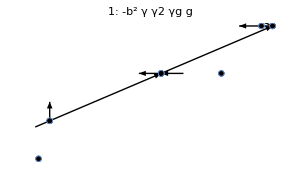
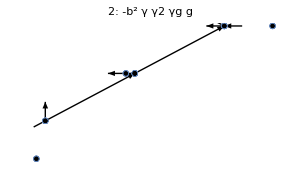
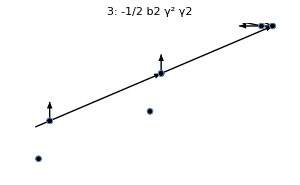
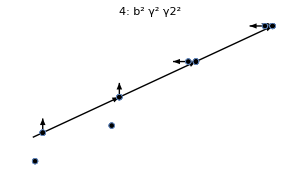
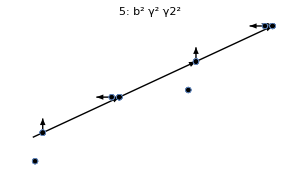

```mathematica
DrawFromContractionGeneral[(TwoLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### TwoLoop: contraction form TwoLoopBackbone

#### Actual computation

```mathematica
(List@@TwoLoopBackbone);
Times[#,Product[Vψχ[Subscript[x,endTime+10+i],endTime+10+i],{i,1,nInteractionVertices-Exponent[#,g]}]]&/@%;
withInteractionVless=%/.V[A_]->A;

WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{ψ,χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%;

twoLoop=Total@%;
twoLoopList=List@@%;

evaluatedResult=EvaluatePropagators[%%];
(*RemoveGaps[%]*)

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(twoLoopList);
RemoveGaps[EvaluatePropagators[#]]&/@%;
(%);
DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

!!ZERO!!

$Aborted

```mathematica
evaluatedResult;
RemoveGaps[%];

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(*(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])(*Vψχ[Subscript[x,endTime+100],endTime+1]*)(*δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]]*))])
)*)
GiveInteractionVertices[List@@TwoLoopBackbone];

(*withInteraction=(List@@TwoLoopBackbone);
Times[#,Product[Vψχ[Subscript[x,endTime+10+i],endTime+10+i],{i,1,2-Exponent[#,g]}]]&/@withInteraction;*)

AbsoluteTiming[twoLoopMod=List@@(Plus@@(WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(endTime),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->10]&/@%)(*/.ψs[__]->0*)(*/.V[b]->b/.DD^({0,1})[{0,0}]->1*))]
EvaluatePropagators[%[[2]]]
```

{0.277315,{2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_11,x_3,t_6,t_3] G_ψ[x_11,x_1,t_6,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_11,x_3,t_6,t_3] G_ψ[x_11,x_2,t_6,t_3],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_21,x_3,t_5,t_3] G_ψ[x_21,x_1,t_5,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_21,x_3,t_5,t_3] G_ψ[x_21,x_2,t_5,t_3],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_31,x_3,t_4,t_3] G_ψ[x_31,x_1,t_4,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_31,x_3,t_4,t_3] G_ψ[x_31,x_2,t_4,t_3],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_41,x_3,t_3,t_3] G_ψ[x_41,x_1,t_3,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_41,x_3,t_3,t_3] G_ψ[x_41,x_2,t_3,t_3],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_51,x_3,t_2,t_3] G_ψ[x_51,x_1,t_2,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_51,x_3,t_2,t_3] G_ψ[x_51,x_2,t_2,t_3],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_61,x_3,t_1,t_3] G_ψ[x_61,x_1,t_1,t_2],2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_61,x_3,t_1,t_3] G_ψ[x_61,x_2,t_1,t_3]}}

{2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}],0,2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}],0,2 b2 g γ^2 γ2 ϕs[x_3,t_3] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}],0,2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}],0,0,0,2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}],0}

```mathematica
twoLoopMod;
Total@EvaluatePropagators[%]
DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

2 b2 g γ^2 γ2 ϕs[x_3,t_3] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}]+6 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}]+2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_3] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,{t_3,t_2}]

-Graphics--Graphics--Graphics-

```mathematica
Module[{i,terms,temp1},
terms=EvaluatePropagators[twoLoopMod[[1]]];
For[i=1,i<=5,i++,
While[(FreeQ[terms,Subscript[x, i]]),
temp1=terms/.Subscript[x, a_]/;(a>i):>Subscript[x, a-1];
If[temp1===terms, Break[],terms=temp1]
];
];

terms
]
DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

2 b2 g γ^2 γ2 ϕs[x_2,t_4] ψs[x_1,t_3] G_ϕ[x_1,x_3,t_2] G_ϕ[x_2,x_1,t_3] G_ϕ[x_3,x_0,t_1] G_χ[x_3,x_2,t_3] G_ψ[x_3,x_3,{t_3,t_2}]

-Graphics-

```mathematica
Module[{i,terms,temp1},
terms=twoLoopMod;
For[i=1,i<=5,i++,
While[(FreeQ[terms,Subscript[x, i]]),
temp1=terms/.Subscript[x, a_]/;(a>i):>Subscript[x, a-1];
If[temp1===terms, Break[],terms=temp1]
];
];

terms
];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

The following works partially

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(*(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])(*Vψχ[Subscript[x,endTime+100],endTime+1]*)(*δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]]*))])
)*)
GiveInteractionVertices[List@@TwoLoopBackbone];

AbsoluteTiming[TwoLoop=Plus@@(WickContractionSpaceVerticesMODfaster[#,"endTime"->(endTime),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->3]&/@%)(*/.ψs[__]->0*)/.V[b]->b/.Derivative[{0,1}][DD][{0,0}]->1]
```

{29.1792,b^2 g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2]+b^2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3]+b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]+2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3]+2 b2 g γ^2 γ2 V[-g χ[x_11,i_6556,α_6556,t_6] ψ[x_11,t_6]] ϕs[x_3,t_4] ψs[x_1,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3]+b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_2,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_2,x_2,t_5]+2 b2 g γ^2 γ2 V[-g χ[x_11,i_6556,α_6556,t_6] ψ[x_11,t_6]] ϕs[x_3,t_4] ψs[x_2,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_2,x_2,t_5]-b2 γ^2 γ2 V[-g χ[x_11,i_72326,α_72326,t_6] ψ[x_11,t_6]] ϕs[x_3,t_4] ψs[x_1,t_6] ψs[x_2,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_2,x_2,t_5]-b2 γ^2 γ2 V[-g χ[x_11,i_2272,α_2272,t_6] ψ[x_11,t_6]] V[-g χ[x_12,i_38167,α_38167,t_6] ψ[x_12,t_6]] ϕs[x_3,t_4] ψs[x_1,t_6] ψs[x_2,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_2,x_2,t_5]+b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_2,t_2]] DD[G_χ[x_3,x_4,t_4]] ϕs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

```mathematica
(List@@(TwoLoop))[[{4,5}]]
```

{2 b2 g γ^2 γ2 ϕs[x_3,t_4] ψs[x_1,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3],2 b2 g γ^2 γ2 V[-g χ[x_11,i_6556,α_6556,t_6] ψ[x_11,t_6]] ϕs[x_3,t_4] ψs[x_1,t_6] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_1,x_1,t_5] G_ψ[x_2,x_2,t_3]}

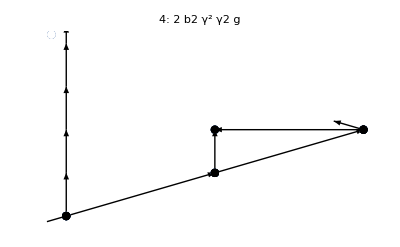
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
List@@(TwoLoop(*/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]]*));
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

```mathematica
(* This looks ok, let's see 2-Loop*)
```

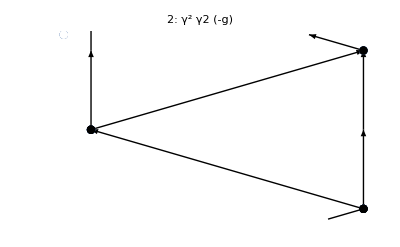
-Graphics--Graphics-

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

## 2-Loop: VERTICES WITH g

### Generate TwoLoopγListCoupling

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Spreadγ[nInteractionVertices-(jjj),"print"->False,
"nγ1δ"->0,"nγ2Minus"->(nInteractionVertices-jjj-2iii),"nγ2Minus2"->(iii),"nγg"->(jjj),"evaluate"->False,"observable"->"g"],
{iii,0,Floor[(nInteractionVertices-jjj)/2]}],
{jjj,0,nInteractionVertices}])
,2]
)
AppendTo[TwoLoopγListCoupling,{Vγ1,Vγg}]
```

{{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγ2Minus1,Vγg},{Vγ1,Vγg,Vγ2Minus1}}

{{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγ2Minus1,Vγg},{Vγ1,Vγg,Vγ2Minus1},{Vγ1,Vγg}}

Manual clean up: no (#γ1 bofore γ2) smaller than #γ2

```mathematica
TwoLoopγListCoupling= Select[TwoLoopγListCoupling,!MatchQ[#,{Vγ1,Vγ2Minus1,___}]&&!MatchQ[#,{a_,Vγ1,Vγ2Minus1,___}]&]
```

{{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγg,Vγ2Minus1},{Vγ1,Vγg}}

### Contract ϕ in TwoLoopγListCoupling -> TwoLoopBackbone

{b g γ γg ϕs[x_2,t_2] χ[x_2,1,α_60899,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],b^2 g^2 γ γ2 γg DD[χs[x_3,1,2,t_3]] ϕs[x_3,t_3] χ[x_1.5,i_47582,α_47582,t_3.5] χ[x_2,1,α_64470,t_2] χs[x_2,1,2,t_2] ψ[x_1.5,t_3.5] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 g^2 γ^2 γ2 DD[χs[x_3,1,1,t_3],χs[x_3,2,2,t_3]] ϕs[x_3,t_3] χ[x_0.5,i_85122,α_85122,t_2.5] χ[x_1.5,i_71385,α_71385,t_3.5] χs[x_0.5,i_85122,α_85122,t_2.5] χs[x_1.5,i_71385,α_71385,t_3.5] ψ[x_0.5,t_2.5] ψ[x_1.5,t_3.5] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],1/2 b^2 g^2 γ^2 γ2^2 DD[χs[x_3,1,2,t_3]] DD[χs[x_4,1,2,t_4]] ϕs[x_4,t_4] χ[x_1.5,i_44205,α_44205,t_3.5] χ[x_2.5,i_22824,α_22824,t_4.5] ψ[x_1.5,t_3.5] ψ[x_2.5,t_4.5] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]}

Some of them are sums!!

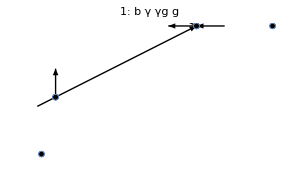
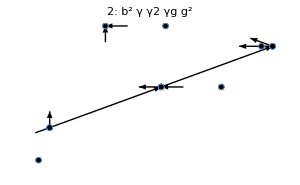
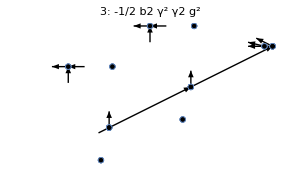
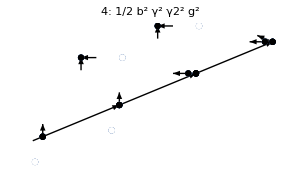

```mathematica
EvaluateVertices[TwoLoopγListCoupling,"Appendϕ0"->True];

((Internal`InheritedBlock[{δ,ϕ,ϕs,x},Clear[δ,ϕ,ϕs,x];
WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%]))/.V[a_]:>a;

TwoLoopBackbone=List@@(Total@(%))/.ϕs[a_,Subscript[t, b_]]:>ϕs[a,Subscript[t, b-1]]

DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### Contract χ TwoLoopBackbone -> TwoLoopBackboneGreen

```mathematica
nInteractionVertices=2;
TwoLoopBackbone;

Times[#,Product[Vψχδ[endTime+nInteractionVertices+iii,endTime+nInteractionVertices+iii],{iii,1,nInteractionVertices-Exponent[#,g]}]]&/@%;
%/.V[a_]->a;

(WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%);
Total@%/.DD[a_,χs[__]]->0;

EvaluatePropagators[%]/.A_. Subscript[G, ϕ][___,Subscript[t, a_]]Subscript[G, ϕ][___,Subscript[t, b_]]/;a==b :>0;
TwoLoopBackboneGreen=Select[List@@(RemoveGaps@%),#=!=0&];
DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

Some of them are sums!!

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* The problem is just in the drawing routine *)
```

```mathematica
TwoLoopBackboneGreen[[6]]
RemoveGaps@%
```

-b g^2 γ γg ϕs[x_2,t_8] ψ[x_8,t_8] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_8] G_χ[x_2,x_8,t_8] G_χ[x_8,x_2,t_8]

-b g^2 γ γg ϕs[x_2,t_2] ψ[x_3,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_2,x_3,t_2] G_χ[x_3,x_2,t_2]

### Contract ψ TwoLoopBackboneGreen -> TwoLoop

```mathematica
TwoLoopBackboneGreen;

WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%;

twoLoop=Total@(%/.DD[a_,χs[__]]->0/.χs[a_,__,Subscript[t, b_]]->χs[a,1,1,Subscript[t, b]]);
twoLoopList=List@@%;

evaluatedResult=EvaluatePropagators[%%];
evaluatedResultList=RemoveGaps/@Select[List@@%,#=!=0&]
(*RemoveGaps[%]*)

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],-b g^2 γ γg ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}

Some of them are sums!!

-Graphics--Graphics--Graphics--Graphics--Graphics-

## 2-Loop: VERTICES WITH g && SpreadγNew

### Generate TwoLoopγListCoupling

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγListCoupling=SpreadγNew[nInteractionVertices]
```

{{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1,Vγ1,Vγg},{1,Vγ1,Vγg,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ2Minus2}}

### Contract ϕ in TwoLoopγListCoupling -> TwoLoopBackbone

{b g γ γg ϕs[x_2,t_2] χ[x_2,1,α_97456,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],b^2 g^2 γ γ2 γg DD[χs[x_3,1,2,t_3]] ϕs[x_3,t_3] χ[x_1.75,i_23344,α_23344,t_3.25] χ[x_2,1,α_85189,t_2] χs[x_2,1,2,t_2] ψ[x_1.75,t_3.25] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 g^2 γ^2 γ2 DD[χs[x_3,1,1,t_3],χs[x_3,2,2,t_3]] ϕs[x_3,t_3] χ[x_0.75,i_19498,α_19498,t_2.75] χ[x_1.75,i_70899,α_70899,t_3.25] χs[x_0.75,i_19498,α_19498,t_2.75] χs[x_1.75,i_70899,α_70899,t_3.25] ψ[x_0.75,t_2.75] ψ[x_1.75,t_3.25] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],1/2 b^2 g^2 γ^2 γ2^2 DD[χs[x_3,1,2,t_3]] DD[χs[x_4,1,2,t_4]] ϕs[x_4,t_4] χ[x_1.75,i_79999,α_79999,t_3.25] χ[x_2.75,i_93380,α_93380,t_4.25] ψ[x_1.75,t_3.25] ψ[x_2.75,t_4.25] ψs[x_1,t_1] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]}

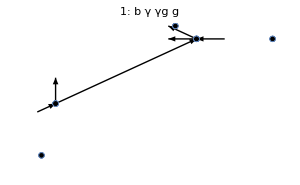
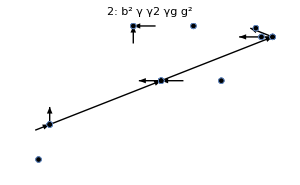
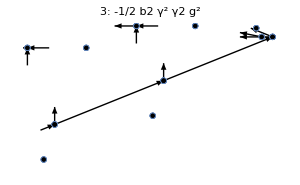
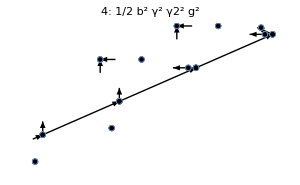

```mathematica
EvaluateVertices[TwoLoopγListCoupling,"Appendϕ0"->True];

((Internal`InheritedBlock[{δ,ϕ,ϕs,x},Clear[δ,ϕ,ϕs,x];
WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%]))/.V[a_]:>a;

TwoLoopBackbone=List@@(Total@(%))/.ϕs[a_,Subscript[t, b_]]:>ϕs[a,Subscript[t, b-1]]

DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### Contract χ TwoLoopBackbone -> TwoLoopBackboneGreen

```mathematica
nInteractionVertices=2;
TwoLoopBackbone;

Times[#,Product[Vψχδ[endTime+nInteractionVertices+iii,endTime+nInteractionVertices+iii],{iii,1,nInteractionVertices-Exponent[#,g]}]]&/@%;
%/.V[a_]->a;

(WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%);
Total@%/.DD[a_,χs[__]]->0;

EvaluatePropagators[%]/.A_. Subscript[G, ϕ][___,Subscript[t, a_]]Subscript[G, ϕ][___,Subscript[t, b_]]/;a==b :>0;
TwoLoopBackboneGreen=Select[List@@(RemoveGaps@%),#=!=0&];
DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* The problem is just in the drawing routine *)
```

### Contract ψ TwoLoopBackboneGreen -> TwoLoop

```mathematica
TwoLoopBackboneGreen;

WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%;

twoLoop=Total@(%/.DD[a_,χs[__]]->0/.χs[a_,__,Subscript[t, b_]]->χs[a,1,1,Subscript[t, b]]);
twoLoopList=List@@%;

evaluatedTwoLoopResult=EvaluatePropagators[%%];
evaluatedTwoLoopResultList=RemoveGaps/@Select[List@@%,#=!=0&]
(*RemoveGaps[%]*)

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],-b g^2 γ γg ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}

-Graphics--Graphics--Graphics--Graphics--Graphics-

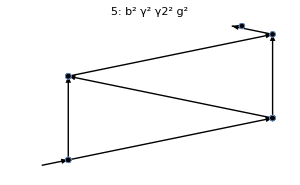
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@Map[DDeatsG,evaluatedTwoLoopResultList]
```

```mathematica
(*CORRECT!!*)
```

## 3-Loop: VERTICES WITH g && SpreadγNew WORK IN PROGRESS

### Generate ThreeLoopγListCoupling PARTIAL LIST: MISSING SOME WITH γ_2^+ (i guess)

```mathematica
nInteractionVertices=3;
nγ2=0;
nγ2Minus=2;
endTime=nInteractionVertices+nInteractionVertices+1;

ThreeLoopγListCoupling=SpreadγNew[nInteractionVertices]
```

{{1/6,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/6,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ2Minus1},{1,Vγ1,Vγ1,Vγg},{1,Vγ1,Vγ1,Vγ2Minus1,Vγg},{1,Vγ1,Vγ1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγ1,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγ2Minus1,Vγg,Vγ2Minus1},{1/2,Vγ1,Vγ1,Vγg,Vγ2Minus1,Vγ2Minus1},{1/2,Vγ1,Vγg,Vγg},{1/2,Vγ1,Vγg,Vγg,Vγ2Minus1},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2},{1,Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1},{1,Vγ1,Vγg,Vγ1,Vγ2Minus2},{1,Vγ1,Vγ1,Vγg,Vγ2Minus2}}

### Contract ϕ in ThreeLoopγListCoupling -> ThreeLoopBackbone

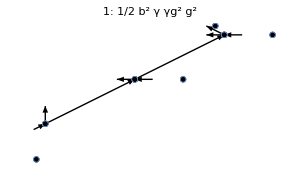
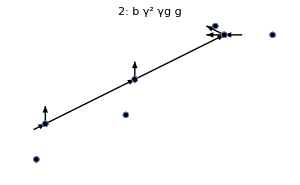
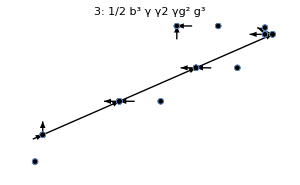
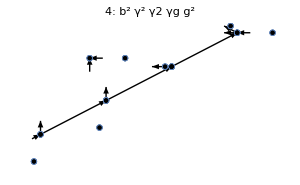
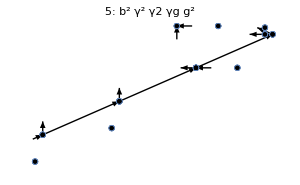
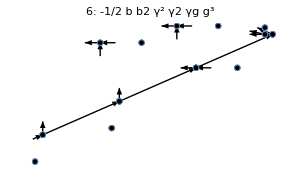
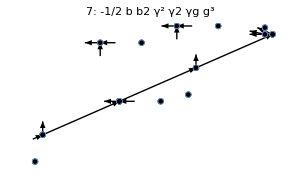
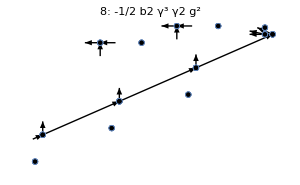

```mathematica
EvaluateVertices[ThreeLoopγListCoupling,"Appendϕ0"->True];

((Internal`InheritedBlock[{δ,ϕ,ϕs,x},Clear[δ,ϕ,ϕs,x];
WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%]))/.V[a_]:>a;

ThreeLoopBackbone=List@@(Total@(%))/.ϕs[a_,Subscript[t, b_]]:>ϕs[a,Subscript[t, b-1]];

DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### Contract χ ThreeLoopBackbone -> ThreeLoopBackboneGreen

```mathematica
nInteractionVertices=2;
ThreeLoopBackbone;

Times[#,Product[Vψχδ[endTime+nInteractionVertices+iii,endTime+nInteractionVertices+iii],{iii,1,nInteractionVertices-Exponent[#,g]}]]&/@%;
toContraction=%/.V[a_]->a;
Length[%]
```

18

```mathematica
temp1to9=(ParallelMap[WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&,toContraction[[1;;9]]]);
ThreeLoopBackboneGreen=Total@%/.DD[a_,χs[__]]->0;
```

```mathematica
temp10to18=(ParallelMap[WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{χ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&,toContraction[[10;;-1]]]);
```

Join::normal: Nonatomic expression expected at position 1 in Join[IterationLimit].

```mathematica
temp
```

temp

```mathematica
ThreeLoopBackboneGreen
```

Total[$Aborted]

```mathematica
List@@ThreeLoopBackboneGreen;

EvaluatePropagators[%];
%/.A_. Subscript[G, ϕ][___,Subscript[t, a_]]Subscript[G, ϕ][___,Subscript[t, b_]]/;a==b :>0;
Select[List@@(RemoveGaps@%),#=!=0&];

DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@%
```

-Graphics-

```mathematica
EvaluatePropagators[%]/.A_. Subscript[G, ϕ][___,Subscript[t, a_]]Subscript[G, ϕ][___,Subscript[t, b_]]/;a==b :>0;
ThreeLoopBackboneGreen=Select[List@@(RemoveGaps@%),#=!=0&];
DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@%
```

$Aborted

Some of them are sums!!

```mathematica
(* The problem is just in the drawing routine *)
```

### Contract ψ ThreeLoopBackboneGreen -> ThreeLoop

```mathematica
TwoLoopBackboneGreen;

WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(10000),"print"->False,"fields"->FieldsNamesGenerator[{ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"maxContractions"->10]&/@%;

twoLoop=Total@(%/.DD[a_,χs[__]]->0/.χs[a_,__,Subscript[t, b_]]->χs[a,1,1,Subscript[t, b]]);
twoLoopList=List@@%;

evaluatedResult=EvaluatePropagators[%%];
evaluatedResultList=RemoveGaps/@Select[List@@%,#=!=0&]
(*RemoveGaps[%]*)

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],-b g^2 γ γg ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}

Some of them are sums!!

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(*CORRECT!!*)
```

# Coupling renormalization

## 1-Loop: SpreadγNew

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=1;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=SpreadγNew[nInteractionVertices]
```

{{Vγg},{Vγ1,Vγ2Minus1}}

```mathematica
ΓString@OneLoopγListCoupling;
EvaluateVertices[OneLoopγListCoupling]
```

{V[b g γg ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_20684,t_1] χs[x_1,1,2,t_1]],V[-b γ2 DD[χs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[-g χ[x_0.75,i_27592,α_27592,t_2.25] ψ[x_0.75,t_2.25]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_1]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackbone

```mathematica
EvaluateVertices[OneLoopγListCoupling];

AbsoluteTiming[
Internal`InheritedBlock[{δ},Clear[δ];OneLoopBackbone=(Total@(WickContractionSpaceVerticesMODfaster[#*ϕs[Subscript[x, 0],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]];

OneLoopBackbone=List@@(Total@(OneLoopBackbone))/.ϕs[a_,Subscript[t, b_]]:>ϕs[a,Subscript[t, b-1]]
```

{b g γg ϕs[x_1,t_1] χ[x_1,1,α_95513,t_1] χs[x_1,1,2,t_1] G_ϕ[x_1,x_0,t_1]-b γ γ2 DD[χs[x_2,1,2,t_2]] V[-g χ[x_0.75,i_97657,α_97657,t_2.25] ψ[x_0.75,t_2.25]] ϕs[x_2,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2]}

{b g γg ϕs[x_1,t_1] χ[x_1,1,α_95513,t_1] χs[x_1,1,2,t_1] G_ϕ[x_1,x_0,t_1],-b γ γ2 DD[χs[x_2,1,2,t_2]] V[-g χ[x_0.75,i_97657,α_97657,t_2.25] ψ[x_0.75,t_2.25]] ϕs[x_2,t_2] ψs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2]}

Some of them are sums!!

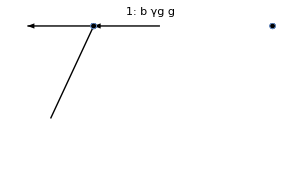
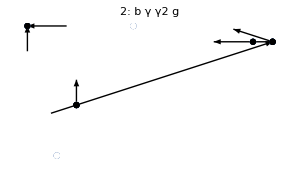

```mathematica
(OneLoopBackbone/.Plus->Sequence)
DrawFromContractionGeneral[(%),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

```mathematica
DrawFromContraction[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&/@(List@@OneLoopBackbone)
```

{-Graphics-,-Graphics-}

### OneLoop: contraction form OneLoopBackbone

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=1;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(*(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])(*Vψχ[Subscript[x,endTime+100],endTime+1]*)(*δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]]*))])
)*)
GiveInteractionVertices[List@@OneLoopBackbone];

AbsoluteTiming[OneLoop=Plus@@(WickContractionSpaceVerticesMODfasterLoc[#,"endTime"->(3),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)(*/.ψs[__]->0*)/.V[b]->b]
```

{0.0353741,b g γg ϕs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1,t_1]+b g γ γ2 DD[G_χ[x_0.75,x_2,t_2.25,t_2]] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_0.75,x_1,t_2.25,t_1]}

```mathematica
OneLoop(*/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]]*);

(%/.DD[a_,χs[__]]->0/.χs[a_,__,Subscript[t, b_]]->χs[a,1,1,Subscript[t, b]]);
OneLoopList=List@@%;

evaluatedResult=EvaluatePropagators[%%];
evaluatedResultList=RemoveGaps/@Select[List@@%,#=!=0&]
(*RemoveGaps[%]*)

DrawFromContractionGeneral[%,"print"->False,"showEndLines"->True,"ImageSize"->300]
```

{b g γg ϕs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1],b g γ γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}]}

Some of them are sums!!

-Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics-

### OneLoop coupling from cutting:

```mathematica
evaluatedResultList
With[{replaced=Level[ReplaceList[#,{A_.Subscript[G, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]/;(b!=0):>A ϕs[Subscript[x, b],Subscript[t, c-1]]ϕ[Subscript[x, a],Subscript[t, c]]}],{1}]},If[replaced==={},{#},replaced]]&/@%
(*(ReplaceList[#,{A_.Subscript[G, ϕ][a__]/;FreeQ[{a},0]:>A}]&/@%)*)
cutResult=Flatten@%
```

{b g γg ϕs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1],b g γ γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}]}

{{b g γg ϕs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1]},{b g γ γ2 DD[G_χ[x_1,x_2,t_2]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,{t_2,t_1}]}}

{b g γg ϕs[x_1,t_1] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1],b g γ γ2 DD[G_χ[x_1,x_2,t_2]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ψ[x_1,x_1,{t_2,t_1}]}

```mathematica
DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@Map[DDeatsG,evaluatedResultList]

DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@cutResult


DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@Map[DDeatsG,cutResult]
```

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

## 2-Loop: Just cut evaluatedTwoLoopResultList

```mathematica
evaluatedTwoLoopResultList
With[{replaced=Level[ReplaceList[#,{A_.Subscript[G, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]/;(b!=0):>A ϕs[Subscript[x, b],Subscript[t, c-1]]ϕ[Subscript[x, a],Subscript[t, c]]}],{1}]},If[replaced==={},{#},replaced]]&/@%
(*(ReplaceList[#,{A_.Subscript[G, ϕ][a__]/;FreeQ[{a},0]:>A}]&/@%)*)
cutTwoLoopResult=Flatten@%
```

{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],-b g^2 γ γg ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}

{{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}]},{-b g^2 γ γg ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}]},{-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}]},{b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_4,t_4] ϕs[x_3,t_3] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}]},{b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_4,t_4] ϕs[x_3,t_3] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}}

{b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],b^2 g^2 γ γ2 γg DD[G_χ[x_1,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,{t_3,t_1}],-b g^2 γ γg ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_2,t_1}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],-2 b2 g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3],G_χ[x_2,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_3,t_3] χs[x_1,1,1,t_3] χs[x_2,1,1,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_4,t_4]] DD[G_χ[x_2,x_3,t_3]] ϕ[x_4,t_4] ϕs[x_3,t_3] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_4,t_1}] G_ψ[x_2,x_2,{t_3,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_2,t_2] ϕs[x_1,t_1] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_3,t_3] ϕs[x_2,t_2] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_4,x_3,t_4] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}],b^2 g^2 γ^2 γ2^2 DD[G_χ[x_1,x_3,t_3]] DD[G_χ[x_2,x_4,t_4]] ϕ[x_4,t_4] ϕs[x_3,t_3] ϕs[x_4,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ψ[x_1,x_1,{t_3,t_1}] G_ψ[x_2,x_2,{t_4,t_2}]}

```mathematica
DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@Map[DDeatsG,evaluatedTwoLoopResultList]

DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@cutTwoLoopResult

DrawFromContractionGeneral[#,"print"->False,"showEndLines"->True,"ImageSize"->300]&@Map[DDeatsG,cutTwoLoopResult]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## 1-Loop: (b=1) (old)

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1}}

```mathematica
ΓString@OneLoopγListCoupling
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγ1δ]+ΓString[Vγ1,Vγ1,Vγ2]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2,Vγ1]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Apply γ1FollowedByγ2p (Rule 2) to OneLoopγListRule1 -> OneLoopγListRule2

```mathematica
OneLoopγListRule2=γ1FollowedByγ2p[OneLoopγListCoupling]
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,-Vγ1δ},{Vγ1,Vγg},{-Vγ1δ,Vγ1},{Vγg,Vγ1}}

```mathematica
ΓString@OneLoopγListRule2
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγg]-ΓString[Vγ1δ,Vγ1]+ΓString[Vγg,Vγ1]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Evaluate the vertices in OneLoopγListRule2 -> OneLoopγListEvaluated

```mathematica
OneLoopγListEvaluated=EvaluateVertices[OneLoopγListRule2]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]],-V[ϕs[x_0,t_1]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackbone

```mathematica
OneLoopγListEvaluated;

AbsoluteTiming[OneLoopBackbone=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.0282247,{g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],g γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],γ^2 ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^2 γ2 DD[δχs[x_2,1,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}}

```mathematica
DrawFromContraction[(OneLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### OneLoop: contraction form OneLoopBackbone

```mathematica
SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True]
```

V[-g χ[x_11,i_65104,α_65104,t_3] χs[x_11,i_65104,α_65104,t_3] ψ[x_11,t_3]]+V[-g χ[x_21,i_91095,α_91095,t_2] χs[x_21,i_91095,α_91095,t_2] ψ[x_21,t_2]]+V[-g χ[x_31,i_55474,α_55474,t_1] χs[x_31,i_55474,α_55474,t_1] ψ[x_31,t_1]]

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[OneLoop=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)/.ψs[__]->0]
```

{5.90453,-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4]-g^2 γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

```mathematica
OneLoop=OneLoop/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## 1-Loop: (b generical) (old)

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1}}

```mathematica
ΓString@OneLoopγListCoupling
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### Apply γ1FollowedByγ2p (Rule 2) to OneLoopγListRule1 -> OneLoopγListRule2

```mathematica
OneLoopγListRule2=γ1FollowedByγ2p[OneLoopγListCoupling]
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,-Vγ1δ},{Vγ1,Vγg},{-Vγ1δ,Vγ1},{Vγg,Vγ1}}

```mathematica
ΓString@OneLoopγListRule2
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### Evaluate the vertices in OneLoopγListRule2 -> OneLoopγListEvaluated

```mathematica
expandedInb=Expandb[ΓString@OneLoopγListRule2]
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1}]

```mathematica
ΓStringExtract/@(List@@expandedInb)
```

{{Vγ1,Vγ1},{Vγ1,Vγg},{-Vγ1δ,-Vγ1},{Vγg,Vγ1},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus2,Vγ1}}

```mathematica
OneLoopγListEvaluatedb=EvaluateVertices[ΓStringExtract/@(List@@expandedInb)]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_19917,t_2] χs[x_2,1,α_19917,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]],V[ϕs[x_0,t_1]] V[b γ δχs[x_1,1,1,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_1689,t_1] χs[x_1,1,α_1689,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-b γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-1/2 b2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-b γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-1/2 b2 γ2 DD[δχs[x_2,1,1,t_2] δχs[x_2,2,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackboneb

```mathematica
OneLoopγListEvaluatedb;

AbsoluteTiming[OneLoopBackboneb=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.030725,{g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_19917,t_2] χs[x_2,1,α_19917,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],g γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χ[x_1,1,α_1689,t_1] χs[x_1,1,α_1689,t_1] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],γ^2 ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],b γ^2 δχs[x_1,1,1,t_1] ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-b γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-b γ^2 γ2 DD[δχs[x_2,1,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 DD[δχs[x_2,1,1,t_2] δχs[x_2,2,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}}

```mathematica
(OneLoopBackboneb)[[6]]
%/.DD[δχs[Subscript[x, a_],A___,Subscript[t, c_]]δχs[Subscript[x, a_],B___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],δχs[Subscript[x, a-0.1],A,Subscript[t, c]]δχs[Subscript[x, a-0.1],B,Subscript[t, c]]}
```

-1/2 b2 γ^2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]

{-1/2 b2 γ^2 γ2 Δ[x_2.9,x_3,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 δχs[x_2.9,1,1,t_3] δχs[x_2.9,2,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}

```mathematica
DrawFromContraction[(OneLoopBackboneb),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### OneLoop: contraction form OneLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(List@@(Plus@@Expand[(OneLoopBackboneb*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[OneLoopb=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)/.ψs[__]->0]
```

{8.85686,-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

```mathematica
OneLoopb=OneLoopb/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

```mathematica
DDeatsG[OneLoopb];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(*OK, CHECK 2LOOP NOW*)
```

## 2-Loop: (b generical) (old)

### TwoLoopBackbone

#### Generate TwoLoopγListCoupling

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγ1δ,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1δ},{Vγ1,Vγ2,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2Minus,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ2,Vγ1,Vγ1}}

```mathematica
ΓString@TwoLoopγListCoupling
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ1δ,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1δ,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1δ,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1δ,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ2,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ2Minus,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1}]

#### Apply γ1FollowedByγ2p (Rule 2) to TwoLoopγListRule1 -> TwoLoopγListRule2

```mathematica
TwoLoopγListRule2=γ1FollowedByγ2p[TwoLoopγListCoupling]
```

{{Vγ1,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ},{Vγ1,Vγ1,Vγg},{Vγ1,-Vγ1δ,Vγ1},{Vγ1,Vγg,Vγ1},{-Vγ1δ,Vγ1,Vγ1},{Vγg,Vγ1,Vγ1},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{Vγ1,Vγ1δ,-Vγ1δ},{Vγ1,Vγ1δ,Vγg},{Vγ1,Vγ1δ,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ},{-Vγ1δ,Vγ1δ,Vγ1},{Vγg,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγg,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγg,Vγ1,Vγ2Minus},{Vγ1,-Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγg,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2Minus,-Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγg},{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1,Vγ2Minus},{Vγg,Vγ1,Vγ1,Vγ2Minus},{-Vγ1δ,Vγ1,Vγ2Minus,Vγ1},{Vγg,Vγ1,Vγ2Minus,Vγ1},{-Vγ1δ,Vγ2Minus,Vγ1,Vγ1},{Vγg,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ2Minus,Vγ1,-Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγg},{Vγ1,Vγ2Minus,-Vγ1δ,Vγ1},{Vγ1,Vγ2Minus,Vγg,Vγ1},{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγg,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγg,Vγ1,Vγ2},{Vγ1,-Vγ1δ,Vγ2,Vγ1},{Vγ1,Vγg,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1,Vγ2},{Vγg,Vγ1,Vγ1,Vγ2},{-Vγ1δ,Vγ1,Vγ2,Vγ1},{Vγg,Vγ1,Vγ2,Vγ1},{-Vγ1δ,Vγ2,Vγ1,Vγ1},{Vγg,Vγ2,Vγ1,Vγ1}}

```mathematica
ΓString@TwoLoopγListRule2
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### SuppressFirstδχ in ΓString@TwoLoopγListRule2 -> SuppressedFirstδχ

```mathematica
SuppressedFirstδχ=SuppressFirstδχ[ΓString@TwoLoopγListRule2]
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγg}]-ΓString[{Vγ1,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγg}]+ΓString[{Vγ1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1δ}]+ΓString[{Vγg,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1δ}]+ΓString[{Vγg,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγg}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus}]-ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγg,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγg,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγg,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1}]

#### Expandb in SuppressedFirstδχ -> expandedInb

```mathematica
expandedInb=Expandb[SuppressedFirstδχ]/.δχ^n_/;n>=3:>0/.δχ:>1;
```

```mathematica
expandedInb
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγg}]-ΓString[{Vγ1,Vγ1δ1,Vγ1δ1}]-ΓString[{Vγ1,Vγ1δ1,Vγ1δ2}]+ΓString[{Vγ1,Vγ1δ1,Vγg}]-ΓString[{Vγ1,Vγ1δ2,Vγ1δ1}]+ΓString[{Vγ1,Vγ1δ2,Vγg}]+ΓString[{Vγ1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1δ1}]+ΓString[{Vγ1,Vγg,Vγ1δ2}]+ΓString[{Vγg,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1δ1}]+ΓString[{Vγg,Vγ1,Vγ1δ2}]+ΓString[{Vγg,Vγ1δ1,Vγ1}]+ΓString[{Vγg,Vγ1δ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγg}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγg}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ22}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus2}]-ΓString[{Vγ1,Vγ1δ1,Vγ1,Vγ21}]-ΓString[{Vγ1,Vγ1δ1,Vγ1,Vγ22}]-ΓString[{Vγ1,Vγ1δ2,Vγ1,Vγ21}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus2,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ21}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ22}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγg,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ22,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus2,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ21}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ22}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγg,Vγ1,Vγ21,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ22,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγg,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ22,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ22}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ22,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ22,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ2Minus1,Vγ1,Vγ1}]

#### Evaluate the vertices in expandedInb -> TwoLoopγListEvaluated

```mathematica
TwoLoopγListEvaluatedb=EvaluateVertices[ΓStringExtract/@(List@@expandedInb)]
```

#### Contract ϕ in TwoLoopγListEvaluated -> TwoLoopBackboneb

```mathematica
TwoLoopγListEvaluatedb;

AbsoluteTiming[TwoLoopBackboneb=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%));]
```

{4.95562,Null}

```mathematica
DrawFromContraction[(TwoLoopBackboneb),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### TwoLoop: contraction form TwoLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

skele=(List@@(Plus@@Expand[(TwoLoopBackboneb*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[TwoLoopb=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,1,500}]);]
```

{67.7903,Null}

```mathematica
AbsoluteTiming[TwoLoopb501=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,501,800}]);]
```

{226.302,Null}

```mathematica
AbsoluteTiming[TwoLoopb801=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,801,900}]);]
```

{1908.94,Null}

```mathematica
AbsoluteTiming[TwoLoopb901=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,901,1000}]);]
```

{989.324,Null}

```mathematica
AbsoluteTiming[TwoLoopb1001=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,1001,Length[skele]}]);]
```

{1385.9,Null}

```mathematica
overall=TwoLoopb+TwoLoopb501+TwoLoopb801+TwoLoopb901+TwoLoopb1001
```

1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,1,t_2] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_4,t_4] G_χ[x_3,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,1,t_3] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_χ[x_3,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_4] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_3,x_3,t_4]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,1,t_3] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_3,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_3,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]

```mathematica
overall=overall/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 5],Subscript[t, 5]]:>χ[Subscript[x, a],Subscript[t, 5]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DDeatsG[overall];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* NO SOME THINGS ARE WRONG !!!*)
```

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the Wolfram cloud.